```mathematica
Exit[]
```

# Black Holes Scalarization

## Reproduce results from Black hole scalarization with Gauss-Bonnet and Ricci Scalar couplings

## Field Equations

## Find the Field Equations

### Call in the Coordinate-Dep. Tensor package, define coordinates and metric

```mathematica
<<xAct`xCoba`;
<<xAct`TexAct`;
DefManifold[MC,4,IndexRange[a,n]]
DefChart[sspher,MC,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Purple]

DefScalarFunction[A]
DefScalarFunction[B]
DefScalarFunction[F]
DefScalarFunction[T]
DefConstantSymbol[α]
DefConstantSymbol[β]
DefConstantSymbol[κ]
DefConstantSymbol[η]

met=CTensor[DiagonalMatrix[{-η Exp[A[r[]]],η Exp[B[r[]]],r[]^2,r[]^2Sin[θ[]]^2}],{-sspher,-sspher}];
SetCMetric[met,sspher,SignatureOfMetric->{3,1,0}];
CD=CovDOfMetric[met];
MetricCompute[met,sspher,All,Parallelize->True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MC.

** DefVBundle: Defining vbundle TangentMC.

** DefChart: Defining chart sspher.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sspher.

** DefMapping: Defining inverse mapping isspher.

** DefTensor: Defining mapping differential tensor disspher[-a,issphera].

** DefTensor: Defining mapping differential tensor dsspher[-a,ssphera].

** DefBasis: Defining basis sspher. Coordinated basis.

** DefCovD: Defining parallel derivative PDsspher[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsspher[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsspher[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsspher[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsspher[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsspher[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsspher[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefScalarFunction: Defining scalar function F.

** DefScalarFunction: Defining scalar function T.

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol κ.

** DefConstantSymbol: Defining constant symbol η.

### Define all the tensors

The Einstein Tensor: G_ab;
Effective Mass Squared for Field Equation : m_eff^2=β/2 R-α𝒢, 𝒢 the Gauss Bonnet Scalar;
The Stress-Energy tensor :(T^ϕ)_μν+(T^α)_μν+ (T^β)_μν, with :
				(T^ϕ)_μν=∇_μ ϕ∇_ν ϕ-1/2 g_μν∇_α ϕ∇^α ϕ , (T^α)_μν=-α/g g_(μ(ρ)g_(σ)ν)ϵ^κραβ ϵ^σγλτ R_λταβ∇_γ ∇_κ ϕ^2, (T^β)_μν= 1/2 β(G_μν-∇_μ ∇_ν +g_μν∇_γ ∇^γ)ϕ^2.

WARNING: Define tensors without “:=”, it does not work properly otherwise!!!

```mathematica
G[a_,b_]=Einstein[CD][a,b];
𝒢 = ((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
meffSqrd = β/2 RicciScalar[CD][]-α((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
TPhi[a_,b_]=
(CD[a]@F[r[]]CD[b]@F[r[]]-1/2 met[a,b]CD[-c]@F[r[]]CD[c]@F[r[]]	
)//ContractBasis;
TBeta[a_,b_] =β(G[a,b](F[r[]])^2/2-CD[a]@CD[b]@((F[r[]])^2/2)+met[a,b]CD[-c]@CD[c]@((F[r[]])^2/2))//ContractBasis;
TAlphaEps[a_,b_] =-α (
2Symmetrize[met[a,-c]met[-d,b],{c,d}]epsilon[met][e,c,f,g]epsilon[met][d,h,i,l]Riemann[CD][-i,-l,-f,-g]CD[-h]@CD[-e]@((F[r[]])^2/2)
)//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];
```

### Field Equations

G_μν=1/2 T_μν     with   T_μν=(T^ϕ)_μν+(T^α)_μν+(T^β)_μν
□ϕ = m_eff^2 ϕ

```mathematica
PhiEq =CD[-a]@CD[a]@F[r[]]-meffSqrd F[r[]];
ttEq=(G[{0,sspher},{0,-sspher}]-  κ SETensor[{0,sspher},{0,-sspher}]);
rrEq=(G[{1,sspher},{1,-sspher}]-  κ SETensor[{1,sspher},{1,-sspher}]);
θθEq=(G[{2,sspher},{2,-sspher}]-  κ SETensor[{2,sspher},{2,-sspher}]);
```

#### Final expression for Eq. of Motion to use in the Numerical Integrator

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ]
FinalϕϕEq = PhiEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalttEq = ttEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalrrEq = rrEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalθθEq = θθEq//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
GaussBonnet = 𝒢//Expand /.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};

FieldEqs = {FinalttEq,FinalrrEq,FinalθθEq,FinalϕϕEq}/.{r[]->r}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r],κ->1/2,η->1};
MatrixForm[FieldEqs]
```

```mathematica
FieldEqs =({{-1/r^2+ⅇ^(-B[r])/r^2+(β ϕ[r]^2)/(4 r^2)-(ⅇ^(-B[r]) β ϕ[r]^2)/(4 r^2)-(ⅇ^(-B[r]) B'[r])/r+(ⅇ^(-B[r]) β ϕ[r]^2 B'[r])/(4 r)-(ⅇ^(-B[r]) β ϕ[r] ϕ'[r])/r+(6 ⅇ^(-2 B[r]) α ϕ[r] B'[r] ϕ'[r])/r^2-(2 ⅇ^(-B[r]) α ϕ[r] B'[r] ϕ'[r])/r^2+1/4 ⅇ^(-B[r]) β ϕ[r] B'[r] ϕ'[r]+1/4 ⅇ^(-B[r]) ϕ'[r]^2-(4 ⅇ^(-2 B[r]) α ϕ'[r]^2)/r^2+(4 ⅇ^(-B[r]) α ϕ'[r]^2)/r^2-1/2 ⅇ^(-B[r]) β ϕ'[r]^2-(4 ⅇ^(-2 B[r]) α ϕ[r] ϕ''[r])/r^2+(4 ⅇ^(-B[r]) α ϕ[r] ϕ''[r])/r^2-1/2 ⅇ^(-B[r]) β ϕ[r] ϕ''[r]}, {-1/r^2+ⅇ^(-B[r])/r^2+(β ϕ[r]^2)/(4 r^2)-(ⅇ^(-B[r]) β ϕ[r]^2)/(4 r^2)+(ⅇ^(-B[r]) A'[r])/r-(ⅇ^(-B[r]) β ϕ[r]^2 A'[r])/(4 r)-(ⅇ^(-B[r]) β ϕ[r] ϕ'[r])/r-(6 ⅇ^(-2 B[r]) α ϕ[r] A'[r] ϕ'[r])/r^2+(2 ⅇ^(-B[r]) α ϕ[r] A'[r] ϕ'[r])/r^2-1/4 ⅇ^(-B[r]) β ϕ[r] A'[r] ϕ'[r]-1/4 ⅇ^(-B[r]) ϕ'[r]^2}, {(ⅇ^(-B[r]) A'[r])/(2 r)-(ⅇ^(-B[r]) β ϕ[r]^2 A'[r])/(8 r)+1/4 ⅇ^(-B[r]) A'[r]^2-1/16 ⅇ^(-B[r]) β ϕ[r]^2 A'[r]^2-(ⅇ^(-B[r]) B'[r])/(2 r)+(ⅇ^(-B[r]) β ϕ[r]^2 B'[r])/(8 r)-1/4 ⅇ^(-B[r]) A'[r] B'[r]+1/16 ⅇ^(-B[r]) β ϕ[r]^2 A'[r] B'[r]-(ⅇ^(-B[r]) β ϕ[r] ϕ'[r])/(2 r)-1/4 ⅇ^(-B[r]) β ϕ[r] A'[r] ϕ'[r]-(ⅇ^(-2 B[r]) α ϕ[r] A'[r]^2 ϕ'[r])/r+1/4 ⅇ^(-B[r]) β ϕ[r] B'[r] ϕ'[r]+(3 ⅇ^(-2 B[r]) α ϕ[r] A'[r] B'[r] ϕ'[r])/r+1/4 ⅇ^(-B[r]) ϕ'[r]^2-1/2 ⅇ^(-B[r]) β ϕ'[r]^2-(2 ⅇ^(-2 B[r]) α A'[r] ϕ'[r]^2)/r+1/2 ⅇ^(-B[r]) A''[r]-1/8 ⅇ^(-B[r]) β ϕ[r]^2 A''[r]-(2 ⅇ^(-2 B[r]) α ϕ[r] ϕ'[r] A''[r])/r-1/2 ⅇ^(-B[r]) β ϕ[r] ϕ''[r]-(2 ⅇ^(-2 B[r]) α ϕ[r] A'[r] ϕ''[r])/r}, {-(β ϕ[r])/r^2+(ⅇ^(-B[r]) β ϕ[r])/r^2+(ⅇ^(-B[r]) β ϕ[r] A'[r])/r+(2 ⅇ^(-2 B[r]) α ϕ[r] A'[r]^2)/r^2-(2 ⅇ^(-B[r]) α ϕ[r] A'[r]^2)/r^2+1/4 ⅇ^(-B[r]) β ϕ[r] A'[r]^2-(ⅇ^(-B[r]) β ϕ[r] B'[r])/r-(6 ⅇ^(-2 B[r]) α ϕ[r] A'[r] B'[r])/r^2+(2 ⅇ^(-B[r]) α ϕ[r] A'[r] B'[r])/r^2-1/4 ⅇ^(-B[r]) β ϕ[r] A'[r] B'[r]+(2 ⅇ^(-B[r]) ϕ'[r])/r+1/2 ⅇ^(-B[r]) A'[r] ϕ'[r]-1/2 ⅇ^(-B[r]) B'[r] ϕ'[r]+(4 ⅇ^(-2 B[r]) α ϕ[r] A''[r])/r^2-(4 ⅇ^(-B[r]) α ϕ[r] A''[r])/r^2+1/2 ⅇ^(-B[r]) β ϕ[r] A''[r]+ⅇ^(-B[r]) ϕ''[r]}});
```

These are transformation law to pass from a coordinate defined as

ⅆ s^2=-ⅇ^A[r]ⅆ t^2+ⅇ^B[r]ⅆ r^2+r^2 ⅆ Ω^2 → ⅆ s^2=-σ[r]ⅆ t^2+(ⅆ r^2)/ρ[r]+r^2 ⅆ Ω^2 .

```mathematica
TrasfAB = {ⅇ^A[r]->A[r],ⅇ^(-B[r])->B[r],ⅇ^(A[r]-2 B[r])->A[r] B[r]^2,ⅇ^(A[r]- B[r])->A[r]B[r],ⅇ^B[r]->B[r]^-1,ⅇ^(2 B[r])->B[r]^-2,B'[r]->-D[Log[B[r]],r],ⅇ^(-B[r])->B[r],A'[r]->D[Log[A[r]],r],ⅇ^(-2 B[r])->B[r]^2,A'[r]^2->D[Log[A[r]],r]^2,A'[r]->D[Log[A[r]],r],B'[r]->-D[Log[B[r]],r],A''[r]->D[Log[A[r]],{r,2}]};
```

## Define the System of Equations for ϕ'', A''

The following steps allows us to get a system of two second order ODE from the four initial field equations. 
First, solve algebraically the rr-equation (get eqs. 24-25) for e^B[r] (i.e. g_rr(r), or (ρ(r))^-1)

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,β,η]
rrSolveEq=FieldEqs[[2]]/.{Exp[B[r]]->h[r],Exp[-B[r]]->(h[r])^-1,Exp[2B[r]]->(h[r])^2,Exp[-2B[r]]->(h[r])^-2,Exp[3B[r]]->(h[r])^3,Exp[6B[r]]->(h[r])^6,Exp[-3B[r]]->(h[r])^-3,Exp[-6B[r]]->(h[r])^-6,η^2->1};
Solve[rrSolveEq==0,h[r]][[2]]
```

{x[r]→1/(2 (-4+β ϕ[r]^2))(-4+β ϕ[r]^2-4 r A'[r]+r β ϕ[r]^2 A'[r]+4 r β ϕ[r] ϕ'[r]-8 α ϕ[r] A'[r] ϕ'[r]+r^2 β ϕ[r] A'[r] ϕ'[r]+r^2 ϕ'[r]^2+√(96 α ϕ[r] (-4+β ϕ[r]^2) A'[r] ϕ'[r]+(4-β ϕ[r]^2+4 r A'[r]-r β ϕ[r]^2 A'[r]-4 r β ϕ[r] ϕ'[r]+8 α ϕ[r] A'[r] ϕ'[r]-r^2 β ϕ[r] A'[r] ϕ'[r]-r^2 ϕ'[r]^2)^2))}

```mathematica
𝒜 =4- β ϕ[r]^2;
ℬ = -4+β ϕ[r]^2+4 r β ϕ[r] ϕ'[r]+r^2 ϕ'[r]^2+A'[r](r^2 β ϕ[r]ϕ'[r]-8 α ϕ[r]ϕ'[r]+r β ϕ[r]^2-4 r );
𝒞 = 24 α A'[r]ϕ[r]ϕ'[r];
rrSolution = (-ℬ+√(ℬ^2-4𝒜 𝒞))/(2𝒜);
```

Hence,the rr-metric coefficient is given by (obtaiend by Trasf of the previous result. )

```mathematica
grr[r_] :=1/(2 (4-β ϕ[r]^2))(4-β ϕ[r]^2-4 r β ϕ[r] ϕ'[r]-r^2 ϕ'[r]^2-(A'[r] (-4 r+r β ϕ[r]^2-8 α ϕ[r] ϕ'[r]+r^2 β ϕ[r] ϕ'[r]))/A[r]+√(-(96 α ϕ[r] (4-β ϕ[r]^2) A'[r] ϕ'[r])/A[r]+(-4+β ϕ[r]^2+4 r β ϕ[r] ϕ'[r]+r^2 ϕ'[r]^2+(A'[r] (-4 r+r β ϕ[r]^2-8 α ϕ[r] ϕ'[r]+r^2 β ϕ[r] ϕ'[r]))/A[r])^2))
```

Then, take the derivative of rr-equation and solve for B’[r], then from θθ-equation get A’’[r] and from the scalar equation get ϕ’’[r].

```mathematica
BPrime = Solve[D[FieldEqs[[2]],r]==0,B'[r]][[1]]//Simplify;
APPrime = Solve[(FieldEqs[[3]]/.BPrime)==0, A''[r]][[1]]//Simplify;
PhiPPrime = Solve[((FieldEqs[[4]]/.BPrime/.APPrime)//Simplify)==0, ϕ''[r]][[1]]//Simplify;
```

Gathering everything together one has that the field equations (eqs 26-27):

```mathematica
PhiEquation = PhiPPrime/.Rule->Subtract;
AEquation = (APPrime/.PhiPPrime//Simplify)/.Rule->Subtract;
ODEqs = {PhiEquation[[1]],AEquation[[1]]}/.{η^2->1};
```

```mathematica
ODEqs={-((ⅇ^(2 B[r]) β^2 ϕ[r]^5 (2 (-1+ⅇ^B[r]) (8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β)+ⅇ^B[r] (-3+ⅇ^B[r]) r^3 β A'[r]-r^2 (8 (1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]^2-4 r^3 α A'[r]^3)+ⅇ^B[r] β ϕ[r]^4 (-2 ⅇ^B[r] r β (-16 α+ⅇ^(2 B[r]) (-16 α+r^2 (-1+2 β))+ⅇ^B[r] (32 α+r^2 (1+2 β)))+(384 (-1+ⅇ^B[r])^2 α^2-8 ⅇ^B[r] (15+4 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α β+ⅇ^(2 B[r]) r^4 β (-4+(3+ⅇ^B[r]) β)) A'[r]+r (64 (-3-6 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-16 ⅇ^B[r] (1+ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 (-1+β) β) A'[r]^2+4 r^2 α (-8 (3+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]^3) ϕ'[r]+4 ⅇ^(2 B[r]) r^3 ϕ'[r] (-4 ⅇ^B[r] r^2 A'[r]^2+2 ⅇ^B[r] (-4+4 ⅇ^B[r]+r^2 ϕ'[r]^2)-r A'[r] (16 ⅇ^B[r]+(8 α+ⅇ^B[r] (-8 α+r^2 (-1+β))) ϕ'[r]^2))+ϕ[r]^2 ϕ'[r] (-16 ⅇ^B[r] r^2 α (-8 (3+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]^3+ⅇ^B[r] A'[r] (-4 (384 (-1+ⅇ^B[r])^2 α^2-8 ⅇ^B[r] (15+4 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α β+ⅇ^(2 B[r]) r^4 β (-8+(3+ⅇ^B[r]) β))+r^2 (-64 α^2 (27+ⅇ^(2 B[r])+8 ⅇ^B[r] (-1+β)-8 β)-8 ⅇ^B[r] r^2 α (9+ⅇ^B[r]-8 β) β+ⅇ^(2 B[r]) r^4 β (-1+2 β)) ϕ'[r]^2)-4 r A'[r]^2 (ⅇ^B[r] (64 (-3-6 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-16 ⅇ^B[r] (1+ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 (-2+β) β)+2 α (-192 α^2+16 ⅇ^B[r] α (8 α-r^2 (-3+β))+ⅇ^(2 B[r]) (-8 α+r^2 β)^2) ϕ'[r]^2)+2 ⅇ^(2 B[r]) r β (8 (-8 α+ⅇ^(2 B[r]) (-8 α+r^2 (-1+β))+ⅇ^B[r] (16 α+r^2 (1+β)))+r^2 (-80 α+ⅇ^B[r] (-16 α+r^2 (-1+2 β))) ϕ'[r]^2))+ⅇ^B[r] ϕ[r]^3 (8 r α A'[r]^3 (4 ⅇ^B[r] r^2 β+(8 α-r^2 β) (8 (-3+ⅇ^B[r]) α-ⅇ^B[r] r^2 β) ϕ'[r]^2)+r β A'[r] (-8 ⅇ^(2 B[r]) (-3+ⅇ^B[r]) r^2 β+(-832 α^2-16 ⅇ^B[r] α (88 α+r^2 (11-16 β))+ⅇ^(2 B[r]) (192 α^2+32 r^2 α (1-3 β)+3 r^4 β (-2+3 β))) ϕ'[r]^2)+A'[r]^2 (8 ⅇ^B[r] r^2 β (8 (1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β)+(2048 (-3+ⅇ^B[r]) α^3+128 (4-7 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α^2 β+ⅇ^(2 B[r]) r^6 β^2 (-1+2 β)-8 ⅇ^B[r] r^4 α β (6-10 β+ⅇ^B[r] (-1+4 β))) ϕ'[r]^2)-2 ⅇ^B[r] β (8 (-1+ⅇ^B[r]) (8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β)-r^2 (ⅇ^B[r] r^2 β (-5+8 β)-8 α (1+8 β+ⅇ^B[r] (-1+8 β))) ϕ'[r]^2))+4 ⅇ^B[r] ϕ[r] (-16 ⅇ^B[r] r^3 α A'[r]^3+r^2 A'[r]^2 (-4 ⅇ^B[r] (8 (1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β)+(-128 α^2+16 ⅇ^B[r] α (8 α-r^2 (-3+β))+ⅇ^(2 B[r]) r^2 (-8 α+r^2 β)) ϕ'[r]^2)+2 ⅇ^B[r] (4 (-1+ⅇ^B[r]) (8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β)+r^2 (-8 (-1+ⅇ^B[r]) α+5 ⅇ^B[r] r^2 β) ϕ'[r]^2-4 r^4 α ϕ'[r]^4)+r A'[r] (4 ⅇ^(2 B[r]) (-3+ⅇ^B[r]) r^2 β+(64 α^2-16 ⅇ^B[r] α (8 α+r^2 (-11+β))+ⅇ^(2 B[r]) (64 α^2+16 r^2 α (-2+β)-3 r^4 (-2+β) β)) ϕ'[r]^2+4 r^2 α (8 α+ⅇ^B[r] (-8 α+r^2 (-1+β))) ϕ'[r]^4)))/(r A'[r] (16 ⅇ^(3 B[r]) r^4+ⅇ^B[r] β ϕ[r]^4 (64 (-1+ⅇ^B[r])^2 α^2+16 ⅇ^B[r] (-1+ⅇ^B[r]) r^2 α β-ⅇ^(2 B[r]) r^4 β (-1+3 β)-16 r α (-8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r])-128 ⅇ^(2 B[r]) r^3 α ϕ[r] ϕ'[r]+8 α ϕ[r]^3 (-4 ⅇ^B[r] r β (16 α+ⅇ^B[r] (-16 α+r^2 (-1+2 β)))+(64 (-3+2 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-16 ⅇ^B[r] (1+ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 β^2) A'[r]) ϕ'[r]-4 ⅇ^B[r] ϕ[r]^2 (64 α^2-128 ⅇ^B[r] α^2+64 ⅇ^(2 B[r]) α^2+2 ⅇ^(2 B[r]) r^4 β-16 ⅇ^B[r] r^2 α β+16 ⅇ^(2 B[r]) r^2 α β-3 ⅇ^(2 B[r]) r^4 β^2-16 r α (-8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]-64 r^2 α^2 ϕ'[r]^2))))+ϕ''[r],-((ⅇ^B[r] β ϕ[r]^4 (-4 ⅇ^(2 B[r]) (-1+ⅇ^B[r]) r^2 β (-1+4 β)-2 ⅇ^B[r] r β (-72 α+ⅇ^B[r] (80 α+r^2 (3-11 β))+ⅇ^(2 B[r]) (-8 α+r^2 (-1+3 β))) A'[r]+(128 (3-4 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-8 ⅇ^B[r] (-23+6 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α β+ⅇ^(2 B[r]) r^4 β (-4+(11+ⅇ^B[r]) β)) A'[r]^2+r (-64 (-7+3 ⅇ^B[r]) α^2-8 ⅇ^B[r] (-11+2 ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 β (-1+2 β)) A'[r]^3+4 r^2 α (-8 (-5+3 ⅇ^B[r]) α+3 ⅇ^B[r] r^2 β) A'[r]^4)+ϕ[r]^3 (16 ⅇ^(3 B[r]) r^3 β^2 (-1+4 β)+4 ⅇ^(2 B[r]) r^2 β (ⅇ^B[r] r^2 β (-3+10 β)-16 α (3-18 β+ⅇ^B[r] (-2+6 β))) A'[r]+2 ⅇ^B[r] r β (2880 α^2-8 ⅇ^B[r] α (176 α+r^2 (9-34 β))+ⅇ^(2 B[r]) (64 α^2+r^4 β (-3+7 β)-8 r^2 α (-3+8 β))) A'[r]^2+(1024 (-3+ⅇ^B[r])^2 α^3+128 ⅇ^B[r] (17-8 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α^2 β+ⅇ^(3 B[r]) r^6 β^2 (-1+2 β)-8 ⅇ^(2 B[r]) r^4 α β (5-14 β+ⅇ^B[r] (-1+4 β))) A'[r]^3+256 r α^2 ((12-8 ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]^4) ϕ'[r]+4 ⅇ^(2 B[r]) r^2 ϕ[r] ϕ'[r] (16 ⅇ^B[r] r β+r^2 (-8 (-5+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]^3+2 r A'[r]^2 (-24 (-3+ⅇ^B[r]) α+3 ⅇ^B[r] r^2 β+4 α (-8 α+r^2 (-1+β)) ϕ'[r]^2)-4 A'[r] (16 (-3+2 ⅇ^B[r]) α-3 ⅇ^B[r] r^2 β+2 r^2 α (1+2 β) ϕ'[r]^2))+4 ⅇ^(2 B[r]) r^2 (-4 ⅇ^B[r] r^3 A'[r]^3+4 ⅇ^B[r] (-4+4 ⅇ^B[r]+r^2 ϕ'[r]^2)-r^2 A'[r]^2 (16 ⅇ^B[r]+(-8 α+ⅇ^B[r] (-8 α+r^2 (-1+β))) ϕ'[r]^2)+2 r A'[r] (4 ⅇ^B[r] (-3+ⅇ^B[r])+(-8 α+ⅇ^B[r] (8 α+r^2 (1+β))) ϕ'[r]^2))-ⅇ^B[r] ϕ[r]^2 (16 r^2 α (-8 (-5+3 ⅇ^B[r]) α+3 ⅇ^B[r] r^2 β) A'[r]^4-4 ⅇ^(2 B[r]) r^2 β (8 (-1+ⅇ^B[r]) (-1+2 β)+r^2 (-1+4 β) ϕ'[r]^2)+8 r A'[r]^3 (-32 (-7+3 ⅇ^B[r]) α^2-4 ⅇ^B[r] (-11+2 ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 (-1+β) β+r^2 α (-8 (-5+3 ⅇ^B[r]) α+3 ⅇ^B[r] r^2 β) ϕ'[r]^2)+A'[r]^2 (4 (128 (3-4 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-8 ⅇ^B[r] (-23+6 ⅇ^B[r]+ⅇ^(2 B[r])) r^2 α β+ⅇ^(2 B[r]) r^4 β (-8+(11+ⅇ^B[r]) β))-r^2 (-64 (21-18 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-8 ⅇ^B[r] (9+ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 β (-1+2 β)) ϕ'[r]^2)-2 ⅇ^B[r] r β A'[r] (4 (-72 α+ⅇ^B[r] (80 α+r^2 (6-11 β))+ⅇ^(2 B[r]) (-8 α+r^2 (-2+3 β)))+r^2 (-24 α+ⅇ^B[r] (-8 α+r^2 (-1+3 β))) ϕ'[r]^2)))/(r A'[r] (16 ⅇ^(3 B[r]) r^4+ⅇ^B[r] β ϕ[r]^4 (64 (-1+ⅇ^B[r])^2 α^2+16 ⅇ^B[r] (-1+ⅇ^B[r]) r^2 α β-ⅇ^(2 B[r]) r^4 β (-1+3 β)-16 r α (-8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r])-128 ⅇ^(2 B[r]) r^3 α ϕ[r] ϕ'[r]+8 α ϕ[r]^3 (-4 ⅇ^B[r] r β (16 α+ⅇ^B[r] (-16 α+r^2 (-1+2 β)))+(64 (-3+2 ⅇ^B[r]+ⅇ^(2 B[r])) α^2-16 ⅇ^B[r] (1+ⅇ^B[r]) r^2 α β+ⅇ^(2 B[r]) r^4 β^2) A'[r]) ϕ'[r]-4 ⅇ^B[r] ϕ[r]^2 (64 α^2-128 ⅇ^B[r] α^2+64 ⅇ^(2 B[r]) α^2+2 ⅇ^(2 B[r]) r^4 β-16 ⅇ^B[r] r^2 α β+16 ⅇ^(2 B[r]) r^2 α β-3 ⅇ^(2 B[r]) r^4 β^2-16 r α (-8 (-1+ⅇ^B[r]) α+ⅇ^B[r] r^2 β) A'[r]-64 r^2 α^2 ϕ'[r]^2))))+A''[r]};
```

```mathematica
Clear[A,B,ϕ,σ,ρ,x,y]
AlgebSystem=Solve[(FieldEqs/.TrasfAB)==0,{ϕ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;3]]/.{Rule->Subtract};
```

## Stability Analysis

## Schwartzchild zero-backreaction limit

In order to study the radial stability, let’s expand the scalar field equation on a fixed Schw. Background. Here we can expand the field on the spherical basis

ϕ[t,r,Ω] = ψ[t,r]/r(Y^m)_l[Ω].

For the radial perturbations the spherical harmonics reduce to a constant. Hence let’s explicit the equation:

```mathematica
(CD[-a]@CD[a]@(F[t[],r[]]/r[])-(-α GG)F[t[],r[]]/r[]==0)/.{r[]->r,t[]->t,η->1}//FullSimplify
```

2 GG α F[t,r]+(ⅇ^(-B[r]) (-(A'[r]-B'[r]) (F[t,r]-r F^(0,1)[t,r])+2 r F^(0,2)[t,r]))/r==2 ⅇ^(-A[r]) F^(2,0)[t,r]

```mathematica
RadialEq=ⅇ^A[r]( GG α F[t,r]+(ⅇ^(-B[r]) (-(A'[r]-B'[r]) (F[t,r]-r Derivative[0,1][F][t,r]) ))/(2 r))==Derivative[2,0][F][t,r]-ⅇ^(A[r]-B[r])Derivative[0,2][F][t,r];
```

Here the effective mass contains only the GB term, since R=0 in Schw. In order to get rid of the first derivative terms, we can introduce the turquoise coordinate defined as

ⅆr = ⅆ r_* √(g_tt/g_rr)=ⅆ r_*ⅇ^((A-B)/2)  ⟹
 ⅆψ/ⅆr=ⅇ^(-(A-B)/2) ⅆψ/(ⅆ r_*) ;(ⅆ^2 ψ)/(ⅆ r^2)= (B'-A')/2 ⅆψ/ⅆr+ⅇ^(B-A)(ⅆ^2 ψ)/(ⅆ(r_*)^2).

Hence, we have (the second derivative of the radial component sis w.r.t. r_*):

```mathematica
(2 GG α F[t,r]+(ⅇ^(-B[r]) (-(A'[r]-B'[r]) (F[t,r]-r Derivative[0,1][F][t,r])+2 r Derivative[0,2][F][t,r]))/r==2 ⅇ^(-A[r]) Derivative[2,0][F][t,r])/.{
F[t,r]->ψ[t,r],
 Derivative[2,0][F][t,r]-> D[D[( ψ[t,r]), t], t],
Derivative[0,1][F][t,r]->(D[ψ[t,r], r]),
 Derivative[0,2][F][t,r]->(Exp[(B[r[]]-A[r[]])]D[D[ψ[t,r], r], r]+1/2(B'[r[]]-A'[r[]])D[ψ[t,r], r])}
```

2 GG α ψ[t,r]+1/r ⅇ^(-B[r]) ((-A'[r]+B'[r]) (ψ[t,r]-r ψ^(0,1)[t,r])+2 r (1/2 (-A'[r]+B'[r]) ψ^(0,1)[t,r]+ⅇ^(-A[r]+B[r]) ψ^(0,2)[t,r]))==2 ⅇ^(-A[r]) ψ^(2,0)[t,r]

And it can be recast as follows

```mathematica
(- ψ[t,r] ⅇ^A[r]/(r 2 ⅇ^B[r]) (2 ⅇ^B[r] r (-α GG)+A'[r]-B'[r])+ Derivative[0,2][ψ][t,r]- Derivative[2,0][ψ][t,r]==0)//Simplify
```

(ⅇ^(A[r]-B[r]) ψ[t,r] (2 ⅇ^B[r] GG r α-A'[r]+B'[r]))/(2 r)+ψ^(0,2)[t,r]==ψ^(2,0)[t,r]

The equation is in the form of a Schrödinger Equation

-(ⅆ^2 ψ)/(ⅆ t^2) + (ⅆ^2 ψ)/(ⅆ(r_*)^2) = V_eff ψ ; V_eff = ⅇ^A[r](-α 𝒢+(A'[r]-B'[r])/(2r)ⅇ^(-B[r]));

Now let’s explicit the Schw. Component as follows

ⅇ^A[r]=1-(2M)/r ; ⅇ^B[r]=(1-(2M)/r)^-1 ⟹ 𝒢 = (48 M^2)/r^6; V_eff= (1-(2M)/r)(-α (48 M^2)/r^6+M/r^3).

```mathematica
TrasfShw = TrasfAB/.{Exp[-A[r]]->(A[r])^-1}/.{B[r]->A[r],B'[r]->A'[r]}/.{Exp[-A[r]]->(A[r])^-1}/.{1/A[r]->(1-(2M)/r)^-1,A[r]->(1-(2M)/r),A'[r]->D[(1-(2M)/r),r],A''[r]->D[D[(1-(2M)/r),r],r]};
```

```mathematica
𝒢/.{r[]->r,η->1}/.TrasfShw//Simplify
```

(48 M^2)/r^6

Let’s express the time dependence of the field as an eigenvalues problem.

ψ[t,r]=ψ[r]ⅇ^-ⅈωt→ (ⅆ^2 ψ)/(ⅆ(r_*)^2) =  (V_eff-ω^2)ψ,

anyway, let’s go back to the expression in term of the ordinary radius. We have

```mathematica
RadialEq/.{GG->𝒢}/.{r[]->r,η->1}/.TrasfShw//Simplify
```

((-2 M+r)^2 F^(0,2)[t,r])/r^2==(2 M (2 M-r) (-(r^3-24 M α) F[t,r]+r^4 F^(0,1)[t,r]))/r^7+F^(2,0)[t,r]

We  have the differential equation

(1-(2M)/r)^2∂^2/(∂r^2)ψ = (2M)/r^3(1-(2M)/r)[(1-(24M)/r^2)ψ-r∂/(∂r)ψ]+∂^2/(∂t^2)ψ

```mathematica
RadStab[M_,ωs_]:=(
SOL=NDSolve[
{
(1-(2M)/r)ψ''[r]== (2M)/r^3((1-(24M)/r^3)ψ[r]-r ψ'[r]-ωs ψ[r]),
ψ[2M+0.0001]==0.0003,
ψ'[2M+0.0001]==3
},ψ,{r,2M+0.0001,400M}];
{ψ[400M]/.SOL,ψ'[400M]/.SOL}
);
```

```mathematica
RadStab[0.4,-0][[1,1]]
```

69.426

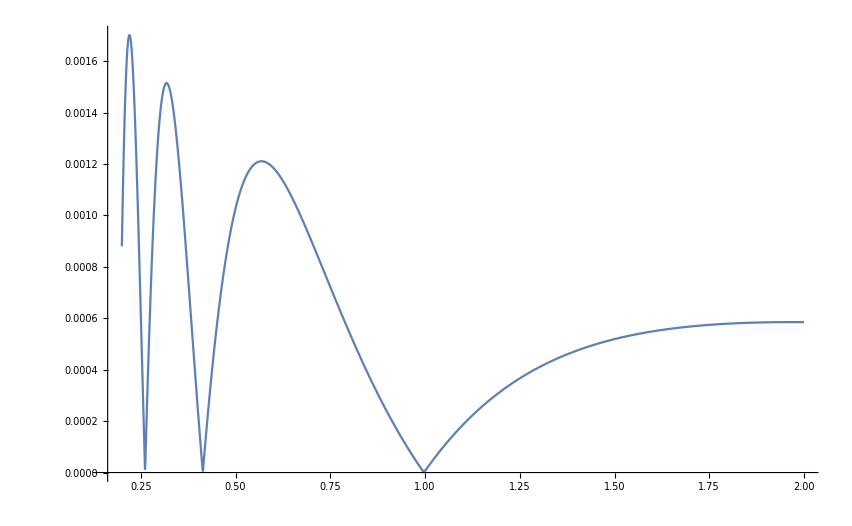

```mathematica
PPP=Table[{t,Abs[RadStab[t,0][[2,1]]]},{t,0.2,2.0,0.001}];
ListPlot[PPP,Joined->True,PlotRange->All]
```

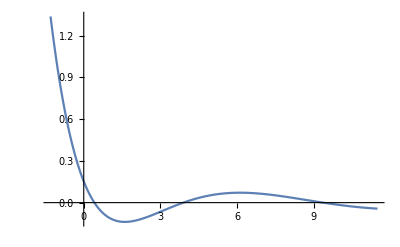

```mathematica
PPP=Table[{t,RadStab[1.2,t][[1,1]]},{t,-1.3,11.5,0.01}];
ListPlot[PPP,Joined->True,PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
Export["Radial.txt",PPP,"Table"]
```

Radial.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Radial.txt"]]]
```

## Metric Perturbations

### Call in the Coordinate-Dep. Tensor package, define coordinates and metric

```mathematica
<<xAct`xCoba`;
<<xAct`TexAct`;
DefManifold[MC,4,IndexRange[a,n]]
DefChart[sspher,MC,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Purple]

DefScalarFunction[A]
DefScalarFunction[B]
DefScalarFunction[F]
DefScalarFunction[T]
DefConstantSymbol[α]
DefConstantSymbol[β]
DefConstantSymbol[κ]
DefConstantSymbol[η]
DefConstantSymbol[ϵ]

DefScalarFunction[Ap]
DefScalarFunction[Bp]
DefScalarFunction[Fp]

met=CTensor[DiagonalMatrix[{-(A[r[]]+ϵ Ap[t[],r[]]),1/(B[r[]]+ϵ Bp[t[],r[]]),r[]^2,r[]^2Sin[θ[]]^2}],{-sspher,-sspher}];
SetCMetric[met,sspher,SignatureOfMetric->{3,1,0}];
CD=CovDOfMetric[met];
MetricCompute[met,sspher,All,Parallelize->True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MC.

** DefVBundle: Defining vbundle TangentMC.

** DefChart: Defining chart sspher.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sspher.

** DefMapping: Defining inverse mapping isspher.

** DefTensor: Defining mapping differential tensor disspher[-a,issphera].

** DefTensor: Defining mapping differential tensor dsspher[-a,ssphera].

** DefBasis: Defining basis sspher. Coordinated basis.

** DefCovD: Defining parallel derivative PDsspher[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsspher[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsspher[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsspher[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsspher[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsspher[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsspher[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefScalarFunction: Defining scalar function F.

** DefScalarFunction: Defining scalar function T.

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol κ.

** DefConstantSymbol: Defining constant symbol η.

** DefConstantSymbol: Defining constant symbol ϵ.

** DefScalarFunction: Defining scalar function Ap.

** DefScalarFunction: Defining scalar function Bp.

** DefScalarFunction: Defining scalar function Fp.

### Define all the tensors

The Einstein Tensor: G_ab;
Effective Mass Squared for Field Equation : m_eff^2=β/2 R-α𝒢, 𝒢 the Gauss Bonnet Scalar;
The Stress-Energy tensor :(T^ϕ)_μν+(T^α)_μν+ (T^β)_μν, with :
				(T^ϕ)_μν=∇_μ ϕ∇_ν ϕ-1/2 g_μν∇_α ϕ∇^α ϕ , (T^α)_μν=-α/g g_(μ(ρ)g_(σ)ν)ϵ^κραβ ϵ^σγλτ R_λταβ∇_γ ∇_κ ϕ^2, (T^β)_μν= 1/2 β(G_μν-∇_μ ∇_ν +g_μν∇_γ ∇^γ)ϕ^2.

WARNING: Define tensors without “:=”, it does not work properly otherwise!!!

```mathematica
G[a_,b_]=Einstein[CD][a,b];
𝒢 = ((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
meffSqrd = β/2 RicciScalar[CD][]-α((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
TPhi[a_,b_]=
(CD[a]@(F[r[]]+ϵ Fp[t[],r[]])CD[b]@(F[r[]]+ϵ Fp[t[],r[]])-1/2 met[a,b]CD[-c]@(F[r[]]+ϵ Fp[t[],r[]])CD[c]@(F[r[]]+ϵ Fp[t[],r[]])	
)//ContractBasis;
TBeta[a_,b_] =β(G[a,b]((F[r[]]+ϵ Fp[t[],r[]]))^2/2-CD[a]@CD[b]@(((F[r[]]+ϵ Fp[t[],r[]]))^2/2)+met[a,b]CD[-c]@CD[c]@(((F[r[]]+ϵ Fp[t[],r[]]))^2/2))//ContractBasis;
TAlphaEps[a_,b_] =-α (
2Symmetrize[met[a,-c]met[-d,b],{c,d}]epsilon[met][e,c,f,g]epsilon[met][d,h,i,l]Riemann[CD][-i,-l,-f,-g]CD[-h]@CD[-e]@(((F[r[]]+ϵ Fp[t[],r[]]))^2/2)
)//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];
```

### Field Equations

G_μν=1/2 T_μν     with   T_μν=(T^ϕ)_μν+(T^α)_μν+(T^β)_μν
□ϕ = m_eff^2 ϕ

```mathematica
PhiEq =CD[-a]@CD[a]@(F[r[]]+ϵ Fp[t[],r[]])-meffSqrd (F[r[]]+ϵ Fp[t[],r[]]);
ttEq=(G[{0,sspher},{0,sspher}]-  κ SETensor[{0,sspher},{0,sspher}]);
trEq=(G[{0,sspher},{1,sspher}]-  κ SETensor[{0,sspher},{1,sspher}]);
rrEq=(G[{1,sspher},{1,sspher}]-  κ SETensor[{1,sspher},{1,sspher}]);
θθEq=(G[{2,sspher},{2,sspher}]-  κ SETensor[{2,sspher},{2,sspher}]);
```

#### Final expression for Eq. of Motion to use in the Numerical Integrator

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,Ap,Bp,Fp]
FinalϕϕEq = PhiEq//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalttEq = ttEq//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinaltrEq = trEq//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalrrEq = rrEq//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
FinalθθEq = θθEq//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};
GaussBonnet = 𝒢//Expand /.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r]};

PerFieldEqs = {FinalttEq,FinaltrEq,FinalrrEq,FinalθθEq,FinalϕϕEq}/.{r[]->r,t[]->t}/.{F[r]->ϕ[r],F'[r]->ϕ'[r],F''[r]->ϕ''[r],κ->1/2,η->1};
PerFieldEqs=Normal[Series[PerFieldEqs,{ϵ,0,1}]]//Simplify;
MatrixForm[PerFieldEqs]
```

```mathematica
PerFieldEqs=({{(-ϵ Ap[t,r] (4-4 r B'[r]+β ϕ[r]^2 (-1+r B'[r])+(-8 α+r^2 β) ϕ[r] B'[r] ϕ'[r]+16 α B[r]^2 (ϕ'[r]^2+ϕ[r] ϕ''[r])+B[r] (-4+β ϕ[r]^2+(-16 α+r^2 (-1+2 β)) ϕ'[r]^2+2 ϕ[r] (2 (r β+6 α B'[r]) ϕ'[r]+(-8 α+r^2 β) ϕ''[r])))+A[r] (4-4 ϵ Bp[t,r]-2 β ϵ Fp[t,r] ϕ[r]-β ϕ[r]^2+β ϵ Bp[t,r] ϕ[r]^2-4 r B'[r]+2 r β ϵ Fp[t,r] ϕ[r] B'[r]+r β ϕ[r]^2 B'[r]+4 r β ϵ Bp[t,r] ϕ[r] ϕ'[r]-8 α ϵ Fp[t,r] B'[r] ϕ'[r]+r^2 β ϵ Fp[t,r] B'[r] ϕ'[r]-8 α ϕ[r] B'[r] ϕ'[r]+r^2 β ϕ[r] B'[r] ϕ'[r]+24 α ϵ Bp[t,r] ϕ[r] B'[r] ϕ'[r]-r^2 ϵ Bp[t,r] ϕ'[r]^2-16 α ϵ Bp[t,r] ϕ'[r]^2+2 r^2 β ϵ Bp[t,r] ϕ'[r]^2-16 α ϵ Bp[t,r] ϕ[r] ϕ''[r]+2 r^2 β ϵ Bp[t,r] ϕ[r] ϕ''[r]-4 r ϵ Derivative[0,1][Bp][t,r]+r β ϵ ϕ[r]^2 Derivative[0,1][Bp][t,r]-8 α ϵ ϕ[r] ϕ'[r] Derivative[0,1][Bp][t,r]+r^2 β ϵ ϕ[r] ϕ'[r] Derivative[0,1][Bp][t,r]-8 α ϵ ϕ[r] B'[r] Derivative[0,1][Fp][t,r]+r^2 β ϵ ϕ[r] B'[r] Derivative[0,1][Fp][t,r]+16 α B[r]^2 (ϕ'[r]^2+ϵ Fp[t,r] ϕ''[r]+2 ϵ ϕ'[r] Derivative[0,1][Fp][t,r]+ϕ[r] (ϕ''[r]+ϵ Derivative[0,2][Fp][t,r]))+B[r] (-4+β ϕ[r]^2-r^2 ϕ'[r]^2-16 α ϕ'[r]^2+2 r^2 β ϕ'[r]^2+32 α ϵ Bp[t,r] ϕ'[r]^2+2 ϵ Fp[t,r] (β ϕ[r]+2 (r β+6 α B'[r]) ϕ'[r]+(-8 α+r^2 β) ϕ''[r])-2 r^2 ϵ ϕ'[r] Derivative[0,1][Fp][t,r]-32 α ϵ ϕ'[r] Derivative[0,1][Fp][t,r]+4 r^2 β ϵ ϕ'[r] Derivative[0,1][Fp][t,r]+2 ϕ[r] ((-8 α+r^2 β+16 α ϵ Bp[t,r]) ϕ''[r]+2 ϕ'[r] (r β+6 α B'[r]+6 α ϵ Derivative[0,1][Bp][t,r])+2 ϵ (r β+6 α B'[r]) Derivative[0,1][Fp][t,r]+(-8 α+r^2 β) ϵ Derivative[0,2][Fp][t,r]))))/(4 r^2 A[r]^2)}, {(ϵ B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r] Derivative[1,0][Fp][t,r]-ϵ A[r] ((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) Derivative[1,0][Bp][t,r]+2 B[r] ((-8 α+r^2 (-1+β)+8 α B[r]) ϕ'[r] Derivative[1,0][Fp][t,r]+(-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[1,1][Fp][t,r])))/(4 r^2 A[r]^2)}, {-(-ϵ Ap[t,r] B[r]^2 A'[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])+A[r]^2 (ϵ Bp[t,r] (4-β ϕ[r]^2)+B[r] (4-2 β ϵ Fp[t,r] ϕ[r]-β ϕ[r]^2+2 ϵ Bp[t,r] (-4+β ϕ[r]^2+4 r β ϕ[r] ϕ'[r]+r^2 ϕ'[r]^2))+B[r]^2 (-4+β ϕ[r]^2+r^2 ϕ'[r]^2+2 β ϵ Fp[t,r] (ϕ[r]+2 r ϕ'[r])+2 r^2 ϵ ϕ'[r] Derivative[0,1][Fp][t,r]+4 r β ϕ[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r])))+A[r] B[r] (24 α B[r]^2 (ϵ Fp[t,r] A'[r] ϕ'[r]+ϕ[r] (ϵ ϕ'[r] Derivative[0,1][Ap][t,r]+A'[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r])))+2 ϵ (Bp[t,r] A'[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β) ϕ[r] ϕ'[r])+(8 α-r^2 β) ϕ[r] Derivative[2,0][Fp][t,r])+B[r] (A'[r] (-4 r+r β ϕ[r]^2+ϵ Fp[t,r] (2 r β ϕ[r]+(-8 α+r^2 β) ϕ'[r])+ϕ[r] ((-8 α+r^2 β+72 α ϵ Bp[t,r]) ϕ'[r]+(-8 α+r^2 β) ϵ Derivative[0,1][Fp][t,r]))+ϵ ((-4 r+r β ϕ[r]^2+(-8 α+r^2 β) ϕ[r] ϕ'[r]) Derivative[0,1][Ap][t,r]-16 α ϕ[r] Derivative[2,0][Fp][t,r]))))/(4 r^2 A[r]^2)}, {-(2 ϵ Ap[t,r] B[r]^2 A'[r]^2 (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r])-A[r] B[r] (ϵ Ap[t,r] (r (-4+β ϕ[r]^2) A'[r] B'[r]+2 B[r] (A'[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+r (-4+β ϕ[r]^2) A''[r])+32 α B[r]^2 (ϕ[r] ϕ'[r] A''[r]+A'[r] (ϕ'[r]^2+ϕ[r] ϕ''[r])))+A'[r] (r ϵ Bp[t,r] (-4+β ϕ[r]^2) A'[r]+B[r] (A'[r] (-4 r+2 r β ϵ Fp[t,r] ϕ[r]+r β ϕ[r]^2+32 α ϵ Bp[t,r] ϕ[r] ϕ'[r])+2 r ϵ (-4+β ϕ[r]^2) Derivative[0,1][Ap][t,r])+16 α B[r]^2 (ϵ Fp[t,r] A'[r] ϕ'[r]+ϕ[r] (2 ϵ ϕ'[r] Derivative[0,1][Ap][t,r]+A'[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r])))))+2 A[r]^3 B[r] (ϵ (Bp[t,r] (2 r (-1+2 β) ϕ'[r]^2+4 β ϕ[r] (ϕ'[r]+r ϕ''[r]))+(-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]) Derivative[0,1][Bp][t,r])+B'[r] (-4+β ϕ[r]^2+2 β ϵ Fp[t,r] (ϕ[r]+r ϕ'[r])+2 r β ϕ[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r]))+B[r] (4 β ϵ Fp[t,r] (ϕ'[r]+r ϕ''[r])+2 r (-1+2 β) ϕ'[r] (ϕ'[r]+2 ϵ Derivative[0,1][Fp][t,r])+4 β ϕ[r] (ϕ'[r]+r ϕ''[r]+ϵ Derivative[0,1][Fp][t,r]+r ϵ Derivative[0,2][Fp][t,r])))+A[r]^2 (2 B[r]^2 ((-4 r+2 r β ϵ Fp[t,r] ϕ[r]+r β ϕ[r]^2+32 α ϵ Bp[t,r] ϕ[r] ϕ'[r]) A''[r]+ϵ (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r]) Derivative[0,1][Ap][t,r]+A'[r] (-4+β ϕ[r]^2+32 α ϵ Bp[t,r] ϕ'[r]^2+2 ϵ Fp[t,r] (β ϕ[r]+(r β+12 α B'[r]) ϕ'[r])+2 ϕ[r] (16 α ϵ Bp[t,r] ϕ''[r]+ϕ'[r] (r β+12 α B'[r]+12 α ϵ Derivative[0,1][Bp][t,r])+ϵ (r β+12 α B'[r]) Derivative[0,1][Fp][t,r]))+r ϵ (-4+β ϕ[r]^2) Derivative[0,2][Ap][t,r])+32 α B[r]^3 (ϵ Fp[t,r] ϕ'[r] A''[r]+ϕ[r] ϕ'[r] A''[r]+ϵ ϕ'[r]^2 Derivative[0,1][Ap][t,r]+ϵ ϕ[r] ϕ''[r] Derivative[0,1][Ap][t,r]+ϵ ϕ[r] A''[r] Derivative[0,1][Fp][t,r]+ϵ ϕ[r] ϕ'[r] Derivative[0,2][Ap][t,r]+A'[r] (ϕ'[r]^2+ϵ Fp[t,r] ϕ''[r]+2 ϵ ϕ'[r] Derivative[0,1][Fp][t,r]+ϕ[r] (ϕ''[r]+ϵ Derivative[0,2][Fp][t,r])))+2 r ϵ (-4+β ϕ[r]^2) Derivative[2,0][Bp][t,r]+B[r] (2 ϵ Bp[t,r] (A'[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+r (-4+β ϕ[r]^2) A''[r])+r A'[r] ((-4+2 β ϵ Fp[t,r] ϕ[r]+β ϕ[r]^2) B'[r]+ϵ (-4+β ϕ[r]^2) Derivative[0,1][Bp][t,r])+ϵ (8 ϕ[r] (4 α ϕ'[r] Derivative[2,0][Bp][t,r]-r β Derivative[2,0][Fp][t,r])+B'[r] (r (-4+β ϕ[r]^2) Derivative[0,1][Ap][t,r]-32 α ϕ[r] Derivative[2,0][Fp][t,r])))))/(16 r^3 A[r]^3 B[r])}, {(2 ϵ Ap[t,r] B[r]^2 (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]^2-A[r] B[r] (ϵ Ap[t,r] ((-8 α+r^2 β) ϕ[r] A'[r] B'[r]+16 α B[r]^2 ϕ[r] A''[r]+2 B[r] (r^2 A'[r] ϕ'[r]+ϕ[r] (2 A'[r] (r β+6 α B'[r])+(-8 α+r^2 β) A''[r])))+A'[r] ((-8 α+r^2 β) ϵ Bp[t,r] ϕ[r] A'[r]+8 α B[r]^2 (ϵ Fp[t,r] A'[r]+ϕ[r] (A'[r]+2 ϵ Derivative[0,1][Ap][t,r]))+B[r] ((-8 α+r^2 β) ϵ Fp[t,r] A'[r]+ϕ[r] ((-8 α+r^2 β+16 α ϵ Bp[t,r]) A'[r]+2 (-8 α+r^2 β) ϵ Derivative[0,1][Ap][t,r]))))+2 A[r]^3 B[r] (2 β ϵ Fp[t,r] (-1+B[r]+r B'[r])+2 β ϕ[r] (-1+B[r]+ϵ Bp[t,r]+r B'[r]+r ϵ Derivative[0,1][Bp][t,r])+r (2 ϵ Bp[t,r] (2 ϕ'[r]+r ϕ''[r])+r ϵ ϕ'[r] Derivative[0,1][Bp][t,r]+r B'[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r])+2 B[r] (2 ϕ'[r]+r ϕ''[r]+2 ϵ Derivative[0,1][Fp][t,r]+r ϵ Derivative[0,2][Fp][t,r])))+A[r]^2 (16 α B[r]^3 (ϵ Fp[t,r] A''[r]+ϕ[r] (A''[r]+ϵ Derivative[0,2][Ap][t,r]))+2 B[r]^2 (ϵ Fp[t,r] (2 A'[r] (r β+6 α B'[r])+(-8 α+r^2 β) A''[r])+r^2 (ϵ ϕ'[r] Derivative[0,1][Ap][t,r]+A'[r] (ϕ'[r]+ϵ Derivative[0,1][Fp][t,r]))+ϕ[r] ((-8 α+r^2 β+16 α ϵ Bp[t,r]) A''[r]+2 ϵ (r β+6 α B'[r]) Derivative[0,1][Ap][t,r]+2 A'[r] (r β+6 α B'[r]+6 α ϵ Derivative[0,1][Bp][t,r])+(-8 α+r^2 β) ϵ Derivative[0,2][Ap][t,r]))+2 (-8 α+r^2 β) ϵ ϕ[r] Derivative[2,0][Bp][t,r]+B[r] ((-8 α+r^2 β) ϵ Fp[t,r] A'[r] B'[r]-8 α ϕ[r] A'[r] B'[r]+r^2 β ϕ[r] A'[r] B'[r]+2 ϵ Bp[t,r] (r^2 A'[r] ϕ'[r]+ϕ[r] (2 A'[r] (r β+6 α B'[r])+(-8 α+r^2 β) A''[r]))-8 α ϵ ϕ[r] B'[r] Derivative[0,1][Ap][t,r]+r^2 β ϵ ϕ[r] B'[r] Derivative[0,1][Ap][t,r]-8 α ϵ ϕ[r] A'[r] Derivative[0,1][Bp][t,r]+r^2 β ϵ ϕ[r] A'[r] Derivative[0,1][Bp][t,r]+16 α ϵ ϕ[r] Derivative[2,0][Bp][t,r]-4 r^2 ϵ Derivative[2,0][Fp][t,r])))/(4 r^2 A[r]^3 B[r])}});
```

### Field Perturbation’s Equations

```mathematica
TrasfN = {ⅇ^A[r]->A[r],ⅇ^(-B[r])->B[r],ⅇ^(A[r]-2 B[r])->A[r] B[r]^2,ⅇ^(A[r]- B[r])->A[r]B[r],ⅇ^B[r]->B[r]^-1,ⅇ^(2 B[r])->B[r]^-2,B'[r]->-D[Log[B[r]],r],ⅇ^(-B[r])->B[r],A'[r]->D[Log[A[r]],r],ⅇ^B[r]->B[r]^-1,ⅇ^(-2 B[r])->B[r]^2,ⅇ^B[r]->B[r]^-1,A'[r]^2->D[Log[A[r]],r]^2,A'[r]->D[Log[A[r]],r],B'[r]->-D[Log[B[r]],r],A''[r]->D[Log[A[r]],{r,2}]};
```

Define variables

```mathematica
varsp={Ap[t,r],Bp[t,r],Fp[t,r]};
varsp=Join[varsp,D[varsp,r],D[varsp,{r,2}],D[varsp,t],D[varsp,{t,2}]];
```

Find system of background equations and solve for second derivatives

```mathematica
BackSystem=Solve[(FieldEqs/.TrasfN)==0,{ϕ''[r],A'[r],B'[r],A''[r]}][[1]];
slo = {BackSystem[[1]], BackSystem[[4]]}//Simplify;
```

```mathematica
Clear[Ap,Bp,Fp,A,B,ϕ,ϵ]
eqper2=Collect[PerFieldEqs//.slo,varsp,Simplify];
```

One can solve for the radial metric component perturbation. The tr-components contains only terms differentiated wrt t, thus one can integrate and solve for Bp

```mathematica
eqper2[[2]]
```

-(ϵ (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) Bp^(1,0)[t,r])/(4 r^2 A[r])+(ϵ B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) Fp^(1,0)[t,r])/(4 r^2 A[r]^2)-(ϵ B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(1,1)[t,r])/(2 r^2 A[r])

Define new rule

```mathematica
Solve[Integrate[eqper2[[2]],t]==0,Bp[t,r]][[1]]//Simplify
```

{Bp[t,r]→(B[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(0,1)[t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))}

```mathematica
D[Bp[t,r]/.ruleBp,r]
```

-((B[r] A'[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(0,1)[t,r]))/(A[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])))+(B'[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(0,1)[t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(B[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+ϕ[r] (2 r β+24 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ''[r]) (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(0,1)[t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2)+(B[r] (Fp[t,r] (ϕ[r] A'[r] (2 r β+8 α B'[r])+2 (r^2+8 α-r^2 β-8 α B[r]) A'[r] ϕ'[r]+(-8 α+r^2 β+8 α B[r]) A'[r] ϕ'[r]+2 A[r] (2 r-2 r β-8 α B'[r]) ϕ'[r]+(-8 α+r^2 β+8 α B[r]) ϕ[r] A''[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ''[r])-2 (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r] Fp^(0,1)[t,r]-2 A[r] ϕ[r] (2 r β+8 α B'[r]) Fp^(0,1)[t,r]-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ'[r] Fp^(0,1)[t,r]+((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) Fp^(0,1)[t,r]-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Fp^(0,2)[t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))

```mathematica
ruleBp= {Bp[t,r]->(B[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[0,1][Fp][t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])),Derivative[0,1][Bp][t,r]-> -((B[r] A'[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[0,1][Fp][t,r]))/(A[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])))+(B'[r] (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[0,1][Fp][t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(B[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+ϕ[r] (2 r β+24 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ''[r]) (Fp[t,r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r])-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[0,1][Fp][t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2)+(B[r] (Fp[t,r] (ϕ[r] A'[r] (2 r β+8 α B'[r])+2 (r^2+8 α-r^2 β-8 α B[r]) A'[r] ϕ'[r]+(-8 α+r^2 β+8 α B[r]) A'[r] ϕ'[r]+2 A[r] (2 r-2 r β-8 α B'[r]) ϕ'[r]+(-8 α+r^2 β+8 α B[r]) ϕ[r] A''[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ''[r])-2 (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r] Derivative[0,1][Fp][t,r]-2 A[r] ϕ[r] (2 r β+8 α B'[r]) Derivative[0,1][Fp][t,r]-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ'[r] Derivative[0,1][Fp][t,r]+((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) Derivative[0,1][Fp][t,r]-2 A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] Derivative[0,2][Fp][t,r]))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))};
```

Apply to the other equations (long but necessary simplify)

```mathematica
eqpsi=Collect[Join[{eqper2[[1]]},eqper2[[3;;5]]]/.ruleBp/.slo,varsp,Simplify];
```

```mathematica
eqh03=Collect[D[eqpsi[[2]],r]/.slo,varsp];
```

```mathematica
soeqs=Solve[eqpsi[[2;;-1]]==0,{Derivative[2,0][Fp][t,r],Derivative[0,1][Ap][t,r],Derivative[0,2][Ap][t,r]}][[1]];
```

Then, the first equation is the desired one

```mathematica
eqph1=Collect[soeqs[[1]]/.Rule->Subtract,varsp,Simplify];
```

```mathematica
eqph1/.{β->0,α->0.1,r->1}
```

(A[1] (-16 ϕ'[1]+4 ϕ[1] (-6.4-0.8 ϕ'[1]^2+3.2 B[1] (2+ϕ'[1]^2))-4 ϕ[1]^2 ϕ'[1] (-0.64-0.8 B[1] (1.6+0.8 ϕ'[1]^2)+0.96 B[1]^2 (2+ϕ'[1]^2))) (1))/(2 ϵ (9+16 1^6 (1.47456 B[1]^6 ϕ'[1]^4+1+3+1-0.064 B[1]^3 (0.+31.744 1^4+2.4 B'[1] (15.36 ϕ'[1]^2+0.64 1^4)))))-(Fp[t,1] (1))/(2 A[1] (1+1))-1/(2 1)-1/1+Fp^(2,0)[t,1]
 |  |  |  |

### Decoupling Limit

Now, we can transform the previous equation in an eigenvalues problem if we chose

Fp[t,r]→ ϕ[r]ⅇ^-iωt→ ∂_tt Fp[t,r]→ -ω^2ϕ[r]

```mathematica
DecRule={Fp[t,r]->ϕp[r],Derivative[0,2][Fp][t,r]->ϕp''[r],Derivative[0,1][Fp][t,r]->ϕp'[r],Derivative[2,0][Fp][t,r]-> -ω^2 ϕp[r]};
```

```mathematica
eqph1/.DecRule
```

```mathematica
EigMode[ωs_,r_]:=-ωs ϕp[r]+(A[r] (-r β^2 (16 α+r^2 β-16 α B[r]) ϕ[r]^5-16 r^4 ϕ'[r]+β (-64 α^2+r^4 (-1+β) β-16 α (8 α+r^2 β) B[r]+192 α^2 B[r]^2) ϕ[r]^4 ϕ'[r]+4 r ϕ[r] (-4 (16 α+r^2 β)+(-8 r^2 α+r^4 β) ϕ'[r]^2+32 α B[r] (2+r^2 ϕ'[r]^2))-4 ϕ[r]^2 ϕ'[r] (-64 α^2+r^4 (-2+β) β+96 α^2 B[r]^2 (2+r^2 ϕ'[r]^2)-8 α B[r] (2 (8 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))+r β ϕ[r]^3 (8 (16 α+r^2 β)+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2-384 α^2 B[r]^2 ϕ'[r]^2+32 α B[r] (-4-(-8 α+r^2 (1+β)) ϕ'[r]^2))) (-3072 r α^3 B[r]^4 ϕ[r]^2 ϕ'[r]^3 (-5 ϕ[r]+2 r ϕ'[r])+r (-4+β ϕ[r]^2) (-16 r^3 (-1+r B'[r])+β ϕ[r]^4 (r (24 α+r^2 (1-3 β)) β-(192 α^2+r^4 (1-3 β) β) B'[r])-4 ϕ[r]^2 (r (24 α+r^2 (2-3 β)) β+(-192 α^2+r^4 β (-2+3 β)) B'[r])+4 r^2 (-8 α+r^2 β) ϕ[r] (-2+r B'[r]) ϕ'[r]+β (192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ[r]^3 (-2+r B'[r]) ϕ'[r])-64 α^2 B[r]^3 ϕ[r] ϕ'[r] (-6 β ϕ[r]^4 (r β-8 α B'[r])+3 r β ϕ[r]^3 (r (-5+4 β)-32 α B'[r]) ϕ'[r]-40 r^3 ϕ'[r]^2+r^2 ϕ[r] ϕ'[r] (60+(-128 α+r^2 (-5+16 β)) ϕ'[r]^2)+4 ϕ[r]^2 (6 r β+r (92 α+r^2 β) ϕ'[r]^2+6 α B'[r] (-8+5 r^2 ϕ'[r]^2)))+B[r] (r β^2 ϕ[r]^6 (-48 r α β+r^3 β (-1+3 β)+384 α^2 B'[r])+2 β ϕ[r]^5 (r β (576 α^2+16 r^2 α (1-6 β)+r^4 β (-1+3 β))-4 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B'[r]) ϕ'[r]+16 r^4 (4+(16 α+r^2 (1-2 β)) ϕ'[r]^2)+8 r^3 ϕ[r] ϕ'[r] (64 α-4 r^2 β-112 r α B'[r]+(-8 α+r^2 β)^2 ϕ'[r]^2)+8 ϕ[r]^3 ϕ'[r] (-r (β (576 α^2+32 r^2 α (1-3 β)+r^4 β (-2+3 β))+2 α (-8 α+r^2 β)^2 ϕ'[r]^2)+α B'[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2))+4 r ϕ[r]^2 (-48 α B'[r] (-32 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+r (12 (-16 α+r^2 (-1+β)) β-(192 α^2+48 r^2 α β+r^4 (2-9 β) β) ϕ'[r]^2))+r β ϕ[r]^4 (48 α B'[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)+r (12 (32 α+r^2 (1-2 β)) β+(192 α^2 (1+4 β)-32 r^2 α β (-1+6 β)+r^4 β (1-7 β+12 β^2)) ϕ'[r]^2)))-8 α B[r]^2 (-3 r β^2 ϕ[r]^6 (r β-8 α B'[r])-2 β ϕ[r]^5 (-72 r α β+r^3 β (-1+6 β)+12 α (32 α+r^2 β) B'[r]) ϕ'[r]+32 r^4 ϕ'[r]^2+16 r^3 ϕ[r] ϕ'[r] (2+(r^2+24 α-3 r^2 β) ϕ'[r]^2)+4 r β ϕ[r]^4 (12 α B'[r] (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+r (6 β+(36 α+r^2 β) ϕ'[r]^2))+2 ϕ[r]^3 ϕ'[r] (-24 α B'[r] (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2)+r (8 β (-36 α+r^2 (-1+3 β))+(-576 α^2+r^4 β (-2+9 β)) ϕ'[r]^2))+r ϕ[r]^2 (-192 α B'[r] (-2+3 r^2 ϕ'[r]^2)+r (-48 β-24 (24 α+r^2 β) ϕ'[r]^2+(256 α^2+8 r^2 α (1-8 β)+r^4 β (-1+4 β)) ϕ'[r]^4)))))/(2 ϵ (1024 r^9+r^2 β^3 ϕ[r]^10 (-r β (6144 α^3+16 r^4 α (1-3 β) β+r^6 (1-3 β)^2 β-64 r^2 α^2 (-4+15 β))-16 α (1536 α^3-192 r^2 α^2 β+8 r^4 α (1-3 β) β+r^6 β^2 (-1+3 β)) B'[r]+6144 α^3 B[r]^3 (r β+4 α B'[r])+64 α^2 B[r]^2 (-288 r α β+r^3 β (-4+15 β)-48 α (24 α-r^2 β) B'[r])+16 α B[r] (r β (1152 α^2-8 r^2 α (-4+15 β)+r^4 (β-3 β^2))+8 α (576 α^2-48 r^2 α β+r^4 (1-3 β) β) B'[r]))-256 r^8 (-8 α+r^2 β+88 α B[r]) ϕ[r] ϕ'[r]-r β^2 ϕ[r]^9 (-12288 α^4 B[r]^4 (23 r β+56 α B'[r])+512 α^3 B[r]^3 (1728 r α β+r^3 (23-84 β) β+96 α (40 α-r^2 β) B'[r])-256 α^2 B[r]^2 (r β (3744 α^2+r^2 α (98-372 β)+r^4 (7-12 β) β)+2 α (3456 α^2-96 r^2 α β+r^4 (17-42 β) β) B'[r])+8 α B[r] (r β (49152 α^3-32 r^4 α β (-7+12 β)-64 r^2 α^2 (-29+120 β)+r^6 β (11-57 β+72 β^2))+48 α (1024 α^3+128 r^2 α^2 β+8 r^4 α (3-10 β) β+3 r^6 β^2 (-1+2 β)) B'[r])+(-8 α+r^2 β) (r β (4608 α^3+24 r^4 α (1-3 β) β+r^6 (1-3 β)^2 β-192 r^2 α^2 (-1+3 β))-8 α (1536 α^3-576 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+9 β)) B'[r])) ϕ'[r]+256 r^5 ϕ[r]^2 (-256 α^2-5 r^4 β-16 r^2 α β+6 r^4 β^2-128 r α^2 B'[r]+16 r^3 α β B'[r]+256 α^3 B[r]^3 ϕ'[r]^2+4 α B[r] (4 (32 α+r^2 β)+32 r α B'[r]+(64 α^2+r^4 β (5+β)-8 r^2 α (5+2 β)) ϕ'[r]^2)-32 α^2 B[r]^2 (8+(16 α-r^2 (25+2 β)) ϕ'[r]^2))-128 r^4 ϕ[r]^3 ϕ'[r] ((8 α-r^2 β) (96 α^2+12 r^2 α β+r^4 (2-3 β) β-4 r α (-8 α+r^2 β) B'[r])+8192 α^4 B[r]^4 ϕ'[r]^2-α B[r] (7424 α^2+896 r^2 α β+4 r^4 (44-57 β) β-576 r α (-8 α+r^2 β) B'[r]+(32 α+r^2 (1-4 β)) (-8 α+r^2 β)^2 ϕ'[r]^2)+16 α^2 B[r]^2 (56 (14 α+r^2 β)+272 r α B'[r]+(768 α^2+r^4 β (17+12 β)-8 r^2 α (17+24 β)) ϕ'[r]^2)-64 α^3 B[r]^3 (92+(288 α-r^2 (115+36 β)) ϕ'[r]^2))+4 β ϕ[r]^8 (147456 α^5 B[r]^5 (5 r β+8 α B'[r]) ϕ'[r]^2-6144 α^4 B[r]^4 (392 r α β+r^3 (5-8 β) β+4 α (128 α+7 r^2 β) B'[r]) ϕ'[r]^2+r β (r^2 β (18432 α^3-16 r^4 α β (-4+9 β)-64 r^2 α^2 (-16+45 β)+r^6 β (5-24 β+27 β^2))-4 α (24 α+r^2 (1-3 β)) (8 α-r^2 β)^3 ϕ'[r]^2+2 r α (8 α-r^2 β) B'[r] (8 (576 α^2+r^4 (4-9 β) β)+(24 α+r^2 (1-3 β)) (-8 α+r^2 β)^2 ϕ'[r]^2))+512 α^3 B[r]^3 (6 α B'[r] (-24 r^2 β+(768 α^2+224 r^2 α β+r^4 (19-40 β) β) ϕ'[r]^2)+r β (-36 r^2 β+(5568 α^2+3 r^4 (13-19 β) β-8 r^2 α (-17+30 β)) ϕ'[r]^2))-32 r α^2 β B[r]^2 (2 r^2 β (-864 α+r^2 (-16+45 β))+(46080 α^3-768 r^2 α^2 (-2+5 β)-24 r^4 α β (-31+50 β)+r^6 β (25-117 β+120 β^2)) ϕ'[r]^2+4 r α B'[r] (72 (-24 α+r^2 β)+(6528 α^2+r^4 β (-65+102 β)-8 r^2 α (-65+204 β)) ϕ'[r]^2))-4 α B[r] (4 α B'[r] (-8 r^2 β (-1728 α^2+144 r^2 α β+r^4 β (-4+9 β))+(-8 α+r^2 β)^2 (384 α^2-192 r^2 α β+r^4 β (-7+18 β)) ϕ'[r]^2)+r β (4 r^2 β (3456 α^2+r^4 (4-9 β) β-8 r^2 α (-16+45 β))+(-86016 α^4+384 r^4 α^2 β (-2+3 β)+3072 r^2 α^3 (-1+6 β)+r^8 β^2 (5-24 β+27 β^2)-8 r^6 α β (5-42 β+60 β^2)) ϕ'[r]^2)))+8 r β ϕ[r]^7 ϕ'[r] ((-8 α+r^2 β) (r β (4608 α^3+36 r^4 α (1-2 β) β-288 r^2 α^2 (-1+2 β)+r^6 β (2-9 β+9 β^2))-12 α (1024 α^3-384 r^2 α^2 β+r^6 (1-2 β) β^2+8 r^4 α β (-1+6 β)) B'[r])-36864 α^5 B[r]^5 (5 r (-1+4 β)+32 α B'[r]) ϕ'[r]^2+16 α^2 B[r]^2 (24 r β (-2496 α^2+r^4 β (-7+8 β)+2 r^2 α (-49+124 β))+r (1024 α^3 (-11+24 β)-256 r^2 α^2 β (-25+36 β)+r^6 β^2 (-17+56 β-48 β^2)+8 r^4 α β (17-134 β+144 β^2)) ϕ'[r]^2+16 α B'[r] (-6912 α^2+192 r^2 α β+3 r^4 β (-17+28 β)+(-8 r α+r^3 β)^2 ϕ'[r]^2))+4096 α^4 B[r]^4 (12 α B'[r] (-14+(64 α+r^2 (7-8 β)) ϕ'[r]^2)+r (-69 β+(r^2 (49-60 β) β+4 α (-31+120 β)) ϕ'[r]^2))+α B[r] (32 α (8 α-r^2 β) B'[r] (6 (256 α^2+64 r^2 α β+3 r^4 (3-4 β) β)+(24 α+r^2 (2-3 β)) (-8 α+r^2 β)^2 ϕ'[r]^2)+r (4 β (98304 α^3-96 r^4 α β (-7+8 β)-192 r^2 α^2 (-29+80 β)+r^6 β (44-171 β+144 β^2))+(-8 α+r^2 β)^2 (16 r^2 α (1-12 β) β+64 α^2 (5+12 β)+r^4 β (1-7 β+12 β^2)) ϕ'[r]^2))-64 α^3 B[r]^3 (192 α B'[r] (-160 α+4 r^2 β+(192 α^2+16 r^2 α (2-3 β)+r^4 β (-4+3 β)) ϕ'[r]^2)+r (12 β (-1152 α+r^2 (-23+56 β))+(-64 r^2 α β (-73+102 β)+128 α^2 (-59+204 β)+r^4 β (115-466 β+408 β^2)) ϕ'[r]^2)))+16 ϕ[r]^6 (1474560 r α^6 B[r]^6 ϕ'[r]^4+49152 α^5 B[r]^5 ϕ'[r]^2 (-15 r β+2 r (-43 α+7 r^2 β) ϕ'[r]^2+3 α B'[r] (-8+5 r^2 ϕ'[r]^2))-r β (r^2 β (18432 α^3-48 r^4 α β (-2+3 β)-192 r^2 α^2 (-8+15 β)+r^6 β (10-36 β+27 β^2))-4 α (24 α+r^2 (2-3 β)) (8 α-r^2 β)^3 ϕ'[r]^2+2 r α (8 α-r^2 β) B'[r] (24 (192 α^2+r^4 (2-3 β) β)+(24 α+r^2 (2-3 β)) (-8 α+r^2 β)^2 ϕ'[r]^2))+256 α^4 B[r]^4 ϕ'[r]^2 (-96 α B'[r] (-128 α-7 r^2 β-4 (-8 r^2 α+r^4 β) ϕ'[r]^2)+r (48 (196 α+r^2 (5-4 β)) β+(17152 α^2-4672 r^2 α β+r^4 β (-133+316 β)) ϕ'[r]^2))-4 r α^2 B[r]^2 (48 r^2 (288 α+r^2 (8-15 β)) β^2-8 β (46080 α^3-768 r^2 α^2 (-4+5 β)-16 r^4 α β (-92+75 β)+r^6 β (75-232 β+120 β^2)) ϕ'[r]^2-(-8 α+r^2 β)^2 (1664 α^2-32 r^2 α β+r^4 (3-22 β) β) ϕ'[r]^4+64 r α B'[r] (-36 β (-24 α+r^2 β)+β (-3264 α^2+r^4 (65-51 β) β+8 r^2 α (-65+102 β)) ϕ'[r]^2-(8 α-r^2 β)^3 ϕ'[r]^4))+4 α B[r] (12 r^3 β^2 (1152 α^2+r^4 (2-3 β) β-8 r^2 α (-8+15 β))+r β (-86016 α^4+6144 r^2 α^3 (-1+3 β)+64 r^4 α^2 β (-23+18 β)+r^8 β^2 (15-47 β+27 β^2)-8 r^6 α β (15-82 β+60 β^2)) ϕ'[r]^2-2 r α (-8 α+r^2 β)^4 ϕ'[r]^4+α B'[r] (-96 r^2 β (-576 α^2+48 r^2 α β+r^4 β (-2+3 β))+8 (-8 α+r^2 β)^2 (192 α^2-96 r^2 α β+r^4 β (-7+9 β)) ϕ'[r]^2+r^2 (-8 α+r^2 β)^4 ϕ'[r]^4))-64 α^3 B[r]^3 (-288 r^3 β^2+4 r β (11136 α^2+32 r^2 α (17-15 β)+r^4 (155-114 β) β) ϕ'[r]^2+(31744 r α^3-9472 r^3 α^2 β+r^7 (25-24 β) β^2+40 r^5 α β (-5+22 β)) ϕ'[r]^4+24 α B'[r] (-48 r^2 β+4 (384 α^2+112 r^2 α β+r^4 (19-20 β) β) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)))+64 r^2 ϕ[r]^4 (86016 r α^5 B[r]^5 ϕ'[r]^4+r (β (6144 α^3+16 r^4 α (4-3 β) β-64 r^2 α^2 (-16+15 β)+r^6 β (10-24 β+9 β^2))-4 α (8 α-r^2 β)^3 ϕ'[r]^2)+2 α (8 α-r^2 β) B'[r] (1536 α^2+8 r^4 (4-3 β) β+(-8 r α+r^3 β)^2 ϕ'[r]^2)+256 r α^4 B[r]^4 ϕ'[r]^2 (-120+(-832 α+r^2 (133+104 β)) ϕ'[r]^2)-4 α^2 B[r]^2 (32 α B'[r] (-576 α+24 r^2 β-65 (-8 r^2 α+r^4 β) ϕ'[r]^2)+r (16 β (-288 α+r^2 (-16+15 β))+8 (1536 α^2+712 r^2 α β+r^4 (75-113 β) β) ϕ'[r]^2+3 (64 α+r^2 (1-8 β)) (-8 α+r^2 β)^2 ϕ'[r]^4))+α B[r] (16 α B'[r] (-8 (576 α^2-48 r^2 α β+r^4 (4-3 β) β)+7 (-8 r α+r^3 β)^2 ϕ'[r]^2)+r (16 β (-1152 α^2+r^4 β (-4+3 β)+8 r^2 α (-16+15 β))+4 (3072 α^3+640 r^2 α^2 β+r^6 β^2 (-15+22 β)-8 r^4 α β (-15+38 β)) ϕ'[r]^2+(-8 α+r^2 β)^4 ϕ'[r]^4))+64 α^3 B[r]^3 (48 α B'[r] (-8+19 r^2 ϕ'[r]^2)+r (-96 β+16 (68 α+19 r^2 β) ϕ'[r]^2+(2688 α^2+r^4 β (25+42 β)-8 r^2 α (25+84 β)) ϕ'[r]^4)))-16 r ϕ[r]^5 ϕ'[r] (3 (-8 α+r^2 β) (r β (1536 α^3-192 r^2 α^2 (-1+β)-24 r^4 α (-1+β) β+r^6 β (2-6 β+3 β^2))-8 α (512 α^3-192 r^2 α^2 β-r^6 (-1+β) β^2+8 r^4 α β (-1+3 β)) B'[r])+589824 r α^6 B[r]^6 ϕ'[r]^4+24576 r α^5 B[r]^5 ϕ'[r]^2 (15+(-64 α+r^2 (5+8 β)) ϕ'[r]^2)+2 α B[r] (12 r β (16384 α^3-32 r^4 α β (-7+4 β)-64 r^2 α^2 (-29+40 β)+r^6 β (22-57 β+24 β^2))-r (-8 α+r^2 β)^2 (-320 α^2-48 r^2 α β+r^4 β (-2+11 β)) ϕ'[r]^2+64 α (8 α-r^2 β) B'[r] (384 α^2+96 r^2 α β+9 r^4 (3-2 β) β+(-8 r α+r^3 β)^2 ϕ'[r]^2))+8 α^2 B[r]^2 (64 α B'[r] (-3456 α^2+96 r^2 α β+3 r^4 β (-17+14 β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+r (96 β (-1248 α^2+r^4 β (-7+4 β)+2 r^2 α (-49+62 β))-8 (5632 α^3-2816 r^2 α^2 β+r^6 (17-22 β) β^2+8 r^4 α β (-17+55 β)) ϕ'[r]^2+(16 α+r^2 (1-2 β)) (8 α-r^2 β)^3 ϕ'[r]^4))-256 α^3 B[r]^3 (192 α B'[r] (-40 α+r^2 β-2 (-8 r^2 α+r^4 β) ϕ'[r]^2)+r (6 β (-576 α+r^2 (-23+28 β))+(-3776 α^2+2192 r^2 α β+5 r^4 (23-43 β) β) ϕ'[r]^2+(32 α+r^2 (1-4 β)) (-8 α+r^2 β)^2 ϕ'[r]^4))+512 α^4 B[r]^4 (1344 α B'[r] (-1+r^2 ϕ'[r]^2)+r (-552 β+(-1984 α+752 r^2 β) ϕ'[r]^2+11 (256 α^2+r^4 β (1+4 β)-8 r^2 (α+8 α β)) ϕ'[r]^4)))))-(ϕp[r] ((-A[r] (2 β A[r] ((-1+B[r]) ϕ[r]+2 r B[r] ϕ'[r])+B[r] A'[r] (2 r β ϕ[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]))-(((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (2 B[r] A'[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+36 α B[r]) ϕ[r] ϕ'[r])+A[r] (4-β ϕ[r]^2+2 B[r] (-4+β ϕ[r]^2+4 r β ϕ[r] ϕ'[r]+r^2 ϕ'[r]^2))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])) (-(-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+A[r] ((-8 α+r^2 β) ϕ[r] B'[r]+2 B[r] (2 ϕ[r] (r β+6 α B'[r])+r^2 ϕ'[r])))+(-8 α+r^2 β+8 α B[r]) ϕ[r] (-2 r B[r] (-4+β ϕ[r]^2) A'[r]+r A[r] (-4+β ϕ[r]^2) B'[r]-32 α B[r]^2 ϕ[r] A'[r] ϕ'[r]+32 α A[r] B[r]^2 ϕ'[r]^2+2 A[r] B[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(32 α A[r] B[r] ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))-B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) ((B[r] A'[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])+(A[r] B'[r] (-(-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (-8 α+r^2 (-1+β)+8 α B[r]) ϕ'[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])+(A[r] B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])) (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+((-8 α+r^2 β+24 α B[r]) ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2-(A[r] B[r] (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])) (2 ϕ[r] A'[r] (r β+4 α B'[r])+2 (8 α-r^2 (-1+β)-8 α B[r]) A'[r] ϕ'[r]+(-8 α+r^2 β+8 α B[r]) A'[r] ϕ'[r]-4 A[r] (r (-1+β)+4 α B'[r]) ϕ'[r]+(2 A[r] (8 α-r^2 (-1+β)-8 α B[r]) (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+(A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])+2 A[r] (r β B[r] ϕ[r] A'[r]^2-r β A[r] ϕ[r] A'[r] B'[r]+8 α B[r]^2 A'[r]^2 ϕ'[r]-2 β A[r]^2 B'[r] (ϕ[r]+r ϕ'[r])-2 A[r] B[r] A'[r] (β ϕ[r]+(r β+12 α B'[r]) ϕ'[r])-(16 α A[r] B[r] A'[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))-(2 r β A[r]^2 ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))-(16 α A[r]^2 ϕ'[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))-4 β A[r]^2 B[r] (ϕ'[r]+(r (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))-(((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (-r B[r] (-4+β ϕ[r]^2) A'[r]^2-32 α B[r]^2 ϕ[r] A'[r]^2 ϕ'[r]+64 α A[r] B[r]^2 A'[r] ϕ'[r]^2+(64 α A[r] B[r] ϕ[r] A'[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))+(64 α A[r]^2 ϕ[r] ϕ'[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+2 A[r] B[r] (A'[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(r A[r] (-4+β ϕ[r]^2) (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))+2 A[r]^2 B[r] (2 r (-1+2 β) ϕ'[r]^2+4 β ϕ[r] (ϕ'[r]+(r (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-B[r] (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (-((B[r] A'[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))+(A[r] B'[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])-(A[r] B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])) (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+((-8 α+r^2 β+24 α B[r]) ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2+(A[r] B[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])) (2 ϕ[r] A'[r] (r β+4 α B'[r])+2 (8 α-r^2 (-1+β)-8 α B[r]) A'[r] ϕ'[r]+(-8 α+r^2 β+8 α B[r]) A'[r] ϕ'[r]-4 A[r] (r (-1+β)+4 α B'[r]) ϕ'[r]+(2 A[r] (8 α-r^2 (-1+β)-8 α B[r]) (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+(A[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])+A[r] ((8 α-r^2 β) B[r] A'[r]^2-8 α B[r]^2 A'[r]^2+(-8 α+r^2 β) A[r] A'[r] B'[r]+4 β A[r]^2 (-1+B[r]+r B'[r])+(16 α A[r]^2 (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+2 A[r] B[r] (2 A'[r] (r β+6 α B'[r])+((-8 α+r^2 β) A[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))+(A[r]^2 B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (4 β ϕ[r]+((8 α-r^2 β) ϕ[r] A'[r]^2)/A[r]^2-(16 α B[r] ϕ[r] A'[r]^2)/A[r]^2+(32 α ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+4 r (2 ϕ'[r]+(r (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))+1/A[r] 2 (r^2 A'[r] ϕ'[r]+ϕ[r] (2 A'[r] (r β+6 α B'[r])+((-8 α+r^2 β) A[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))))/(2 A[r] (2 A[r] B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (2 (-8 α+r^2 β+8 α B[r]) ϕ[r]^2 (r β+4 α B'[r])-r^2 (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]))+(-8 α+r^2 β+8 α B[r]) ϕ[r] ((-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+A[r] ((-8 α+r^2 β) ϕ[r] B'[r]+2 B[r] (2 ϕ[r] (r β+6 α B'[r])+r^2 ϕ'[r])))-(-8 α+r^2 β+8 α B[r]) ϕ[r] (-2 r B[r] (-4+β ϕ[r]^2) A'[r]+r A[r] (-4+β ϕ[r]^2) B'[r]-32 α B[r]^2 ϕ[r] A'[r] ϕ'[r]+32 α A[r] B[r]^2 ϕ'[r]^2+2 A[r] B[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(32 α A[r] B[r] ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))))-(A[r]^2 (1/A[r]^2(-B[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r]))+(2 (-8 α+r^2 β+8 α B[r]) ϕ[r] (2 B[r] A'[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+36 α B[r]) ϕ[r] ϕ'[r])+A[r] (4-β ϕ[r]^2+2 B[r] (-4+β ϕ[r]^2+4 r β ϕ[r] ϕ'[r]+r^2 ϕ'[r]^2))))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])) (-(-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+A[r] ((-8 α+r^2 β) ϕ[r] B'[r]+2 B[r] (2 ϕ[r] (r β+6 α B'[r])+r^2 ϕ'[r])))+(-8 α+r^2 β+8 α B[r]) ϕ[r] (-2 r B[r] (-4+β ϕ[r]^2) A'[r]+r A[r] (-4+β ϕ[r]^2) B'[r]-32 α B[r]^2 ϕ[r] A'[r] ϕ'[r]+32 α A[r] B[r]^2 ϕ'[r]^2+2 A[r] B[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(32 α A[r] B[r] ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))-B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) ((2 (-8 α+r^2 β+8 α B[r]) ϕ[r] B'[r] (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))+(4 B[r] ϕ[r] (r β+4 α B'[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))+(2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ'[r] (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(A[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])) (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+((-8 α+r^2 β+24 α B[r]) ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2)+4 (-2 β B[r] ϕ[r]+(4 α B[r]^2 ϕ[r] A'[r]^2)/A[r]^2-r β ϕ[r] B'[r]-(B[r] ϕ[r] A'[r] (r β+12 α B'[r]))/A[r]-2 r (-1+2 β) B[r] ϕ'[r]-(16 α B[r]^2 A'[r] ϕ'[r])/A[r]-(8 α ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))+(2 (-8 α+r^2 β+8 α B[r]) ϕ[r] (-r B[r] (-4+β ϕ[r]^2) A'[r]^2-32 α B[r]^2 ϕ[r] A'[r]^2 ϕ'[r]+64 α A[r] B[r]^2 A'[r] ϕ'[r]^2+(64 α A[r] B[r] ϕ[r] A'[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))+(64 α A[r]^2 ϕ[r] ϕ'[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/((-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+2 A[r] B[r] (A'[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(r A[r] (-4+β ϕ[r]^2) (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))+2 A[r]^2 B[r] (2 r (-1+2 β) ϕ'[r]^2+4 β ϕ[r] (ϕ'[r]+(r (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))))/(A[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])))-r^2 B[r] (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (2 (B[r] (4/r+A'[r]/A[r])+B'[r])-(2 (-8 α+r^2 β+8 α B[r]) ϕ[r] B'[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(r^2 A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(4 B[r] ϕ[r] (r β+4 α B'[r]) ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(r^2 A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))-(2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ'[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(r^2 A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))+(B[r] ((-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+2 A[r] (r^2+8 α-r^2 β-8 α B[r]) ϕ'[r]) ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(r^2 A[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))+(2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])) (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r]+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r]+(-8 α+r^2 β+24 α B[r]) ϕ'[r]^2+((-8 α+r^2 β+24 α B[r]) ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))/(r^2 A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2)-(2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] (4 β ϕ[r]+((8 α-r^2 β) ϕ[r] A'[r]^2)/A[r]^2-(16 α B[r] ϕ[r] A'[r]^2)/A[r]^2+(32 α ϕ[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))+4 r (2 ϕ'[r]+(r (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(B[r] (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))+1/A[r] 2 (r^2 A'[r] ϕ'[r]+ϕ[r] (2 A'[r] (r β+6 α B'[r])+((-8 α+r^2 β) A[r] (-110592 α^4 B[r]^6 ϕ[r]^3 ϕ'[r]^3 (4 β^2 ϕ[r]^4+r (3-8 β) β ϕ[r]^3 ϕ'[r]+8 r^2 ϕ'[r]^2-8 β ϕ[r]^2 (2+r^2 ϕ'[r]^2)+r ϕ[r] ϕ'[r] (-12+r^2 (-5+8 β) ϕ'[r]^2))-r (8 α-r^2 β) ϕ[r] (-4+β ϕ[r]^2)^2 (-12 α β^2 ϕ[r]^5-16 r^3 ϕ'[r]+4 r (24 α+r^2 (2-3 β)) β ϕ[r]^2 ϕ'[r]+r β^2 (-24 α+r^2 (-1+3 β)) ϕ[r]^4 ϕ'[r]-4 ϕ[r] (48 α+(8 r^2 α-r^4 β) ϕ'[r]^2)+β ϕ[r]^3 (96 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2))+B[r] (-4+β ϕ[r]^2) (2 r β^3 (-192 α^2+30 r^2 α β+r^4 β (-1+3 β)) ϕ[r]^8+2 β^2 (768 α^3-960 r^2 α^2 β+3 r^6 β^2 (-1+3 β)+4 r^4 α β (5+9 β)) ϕ[r]^7 ϕ'[r]-64 r^5 (8+(-8 α+r^2 (-1+β)) ϕ'[r]^2)+32 r^4 ϕ[r] ϕ'[r] (-80 α+12 r^2 β+(-8 α+r^2 β)^2 ϕ'[r]^2)-8 ϕ[r]^3 ϕ'[r] (-12 (256 α^3-320 r^2 α^2 β+3 r^6 (-1+β) β^2+4 r^4 α β (5+3 β))+(8 α+3 r^2 β) (-8 r α+r^3 β)^2 ϕ'[r]^2)+4 β ϕ[r]^5 ϕ'[r] (-6 (512 α^3-640 r^2 α^2 β+3 r^6 β^2 (-1+2 β)+4 r^4 α β (5+6 β))+(-8 r α+r^3 β)^2 (r^2 (1-3 β) β+4 α (1+6 β)) ϕ'[r]^2)+r β^2 ϕ[r]^6 (8 (576 α^2-90 r^2 α β+r^4 (4-9 β) β)+(7680 α^3+r^6 β (-1+3 β)+20 r^4 α β (1+6 β)-32 r^2 α^2 (11+60 β)) ϕ'[r]^2)-4 ϕ[r]^2 (32 (-192 r α^2+30 r^3 α β+r^5 β (-4+3 β))-4 (-352 r^3 α^2+4 r^5 α β+r^7 β (-3+5 β)) ϕ'[r]^2+r^3 (-8 α+r^2 β)^2 (-8 α+r^2 (1+β)) ϕ'[r]^4)+r ϕ[r]^4 (96 β (-192 α^2+30 r^2 α β+r^4 β (-2+3 β))-4 β (7680 α^3+r^6 β (-3+7 β)+8 r^4 α β (4+15 β)-64 r^2 α^2 (11+30 β)) ϕ'[r]^2-(-8 α+r^2 β)^2 (64 α^2-32 r^2 α β+r^4 β (-1+3 β)) ϕ'[r]^4))+B[r]^2 (2 r β^4 (288 α^2-42 r^2 α β+r^4 (1-3 β) β) ϕ[r]^10-β^3 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-1+3 β)+8 r^4 α β (17+24 β)) ϕ[r]^9 ϕ'[r]+r β^3 ϕ[r]^8 (-9216 α^2+1344 r^2 α β+8 r^4 β (-5+12 β)+(-15360 α^3+24 r^4 α β (-23+15 β)+224 r^2 α^2 (13+24 β)+3 r^6 β (1+8 β-33 β^2)) ϕ'[r]^2)-4 β^2 ϕ[r]^7 ϕ'[r] (-18432 α^3+12672 r^2 α^2 β+15 r^6 (4-9 β) β^2-32 r^4 α β (17+18 β)+(12288 α^4-192 r^4 α^2 β (5+6 β)+256 r^2 α^3 (19+24 β)+4 r^6 α β (8+3 β-24 β^2)+r^8 β^2 (-3+4 β+15 β^2)) ϕ'[r]^2)+64 r^5 (-32-4 (16 α+3 r^2 (-1+β)) ϕ'[r]^2+(-8 r^2 α+r^4 (-1+β)) ϕ'[r]^4)-16 r^4 ϕ[r] ϕ'[r] (2176 α-240 r^2 β-16 (64 α^2-32 r^2 α (-1+β)+3 r^4 (-1+β) β) ϕ'[r]^2+(128 r^2 α^2+8 r^4 α (1-4 β)+r^6 β (-1+2 β)) ϕ'[r]^4)+β ϕ[r]^5 ϕ'[r] (-48 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-2+3 β)+16 r^4 α β (17+12 β))+16 (12288 α^4+512 r^2 α^3 (19+12 β)-64 r^4 α^2 β (29+18 β)-8 r^6 α β (-12+β+12 β^2)+r^8 β^2 (-9+11 β+15 β^2)) ϕ'[r]^2+r^4 (-1024 α^3+64 r^2 α^2 β+r^6 (1-3 β) β^2+8 r^4 α β (-1+4 β)) ϕ'[r]^4)+4 ϕ[r]^3 ϕ'[r] (16 (6144 α^3-4224 r^2 α^2 β+15 r^6 β^2 (-4+3 β)+32 r^4 α β (17+6 β))-16 (4864 r^2 α^3-832 r^4 α^2 β+4 r^6 α (24-13 β) β+r^8 β^2 (-9+10 β)) ϕ'[r]^2+r^2 (8192 α^4-1024 r^2 α^3 (-1+6 β)+64 r^4 α^2 β (1+24 β)+r^8 β^2 (-2+5 β+6 β^2)-16 r^6 α β (-1+4 β+10 β^2)) ϕ'[r]^4)+r β ϕ[r]^6 (64 β (864 α^2-126 r^2 α β+r^4 (5-9 β) β)+4 β (30720 α^3-672 r^2 α^2 (13+16 β)-8 r^4 α β (-209+90 β)+3 r^6 β (-4-23 β+66 β^2)) ϕ'[r]^2+(12288 α^4 (5+8 β)-2048 r^2 α^3 β (5+18 β)+r^8 β^2 (1+6 β-27 β^2)-4 r^6 α β^2 (37-128 β+48 β^2)+32 r^4 α^2 β (25-64 β+144 β^2)) ϕ'[r]^4)+4 ϕ[r]^2 (-128 (-288 r α^2+42 r^3 α β+r^5 β (-5+3 β))-16 (2912 r^3 α^2-600 r^5 α β+3 r^7 β (4+5 β)) ϕ'[r]^2-4 (-4096 r^3 α^3+32 r^5 α^2 (-25+62 β)-4 r^7 α β (-33+76 β)+r^9 β (-3-4 β+15 β^2)) ϕ'[r]^4+r^5 (-8 α+r^2 β)^3 ϕ'[r]^6)-4 r ϕ[r]^4 (64 β (576 α^2-84 r^2 α β+r^4 (5-6 β) β)+12 β (5120 α^3-224 r^2 α^2 (13+8 β)-8 r^4 α β (-71+15 β)+3 r^6 β (-2-7 β+11 β^2)) ϕ'[r]^2+(61440 α^4-6144 r^2 α^3 β+48 r^6 α β^2 (-6+17 β)-64 r^4 α^2 β (-25+63 β)+r^8 β^2 (3+11 β-42 β^2)) ϕ'[r]^4+2 r^2 α (-8 α+r^2 β)^3 ϕ'[r]^6))+1536 α^3 B[r]^5 ϕ[r]^2 ϕ'[r] (β^3 ϕ[r]^7-15 r β^3 ϕ[r]^6 ϕ'[r]-12 r^3 ϕ'[r]^3 (-28+r^2 ϕ'[r]^2)+6 β^2 ϕ[r]^5 (-2+(128 α+r^2 (-3+14 β)) ϕ'[r]^2)-2 r β ϕ[r]^4 ϕ'[r] (-60 β+(r^2 β (-51+4 β)+12 α (-7+64 β)) ϕ'[r]^2)-3 β ϕ[r]^3 (-16+16 (64 α+r^2 (-3+7 β)) ϕ'[r]^2-7 (3 r^4-64 r^2 α) ϕ'[r]^4)-3 r ϕ[r]^2 ϕ'[r] (80 β+4 (56 α+41 r^2 β) ϕ'[r]^2+r^2 (α (208-320 β)+r^2 β (-31+40 β)) ϕ'[r]^4)-2 ϕ[r] (32+144 r^2 ϕ'[r]^2-6 (64 r^2 α+3 r^4 (-7+8 β)) ϕ'[r]^4+(-48 r^4 α+r^6 (-5+6 β)) ϕ'[r]^6))+4 α B[r]^3 (3 r β^4 (-32 α+3 r^2 β) ϕ[r]^10+2 β^3 (1152 α^2-432 r^2 α β+r^4 β (11+21 β)) ϕ[r]^9 ϕ'[r]-128 r^5 ϕ'[r]^2 (-12+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^8 (48 (-32 α+3 r^2 β)+(2304 α^2+11 r^4 β (-19+18 β)+24 r^2 α (31+156 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^7 ϕ'[r] (-3456 α^2+1296 r^2 α β-r^4 β (44+63 β)+(12288 α^3+24 r^4 α (-23+β) β+384 r^2 α^2 (4+9 β)+r^6 β (7+39 β-81 β^2)) ϕ'[r]^2)-32 r^4 ϕ[r] ϕ'[r] (-176-16 (44 α+r^2 (-7+6 β)) ϕ'[r]^2+(-64 r^2 α+r^4 (-9+8 β)) ϕ'[r]^4)+r β ϕ[r]^6 (288 β (-32 α+3 r^2 β)+12 β (1536 α^2+24 r^2 α (31+104 β)+r^4 β (-211+132 β)) ϕ'[r]^2+(3072 r^2 α^2 β (7+9 β)-2048 α^3 (31+96 β)+r^6 β^2 (199-260 β-336 β^2)+384 r^4 α β (-4+β+6 β^2)) ϕ'[r]^4)-2 β ϕ[r]^5 ϕ'[r] (-48 (1152 α^2-432 r^2 α β+r^4 β (22+21 β))-16 (-12288 α^3-4 r^4 α β (-287+6 β)-384 r^2 α^2 (8+9 β)+3 r^6 β (-7-24 β+27 β^2)) ϕ'[r]^2+(20480 r^2 α^3-96 r^6 α β (-9+26 β)+192 r^4 α^2 (-23+32 β)+r^8 β (-9-39 β+176 β^2)) ϕ'[r]^4)+8 ϕ[r]^3 ϕ'[r] (-16 (1152 α^2-432 r^2 α β+r^4 β (44+21 β))+16 (1536 r^2 α^2-640 r^4 α β+3 r^6 β (7+9 β)) ϕ'[r]^2+(-4096 r^2 α^3-800 r^6 α β (-1+2 β)+64 r^4 α^2 (-69+112 β)+r^8 β (-18-31 β+96 β^2)) ϕ'[r]^4-r^4 (-8 α+r^2 β)^3 ϕ'[r]^6)+4 ϕ[r]^2 (192 r (-32 α+3 r^2 β)-16 (-744 r^3 α+227 r^5 β) ϕ'[r]^2+(1024 r^3 α^2+4 r^7 (203-198 β) β+64 r^5 α (-96+97 β)) ϕ'[r]^4+(1664 r^5 α^2+r^9 β (-15+26 β)-8 r^7 α (-15+52 β)) ϕ'[r]^6)-r ϕ[r]^4 (768 β (-32 α+3 r^2 β)+48 β (768 α^2+24 r^2 α (31+52 β)+r^4 β (-215+66 β)) ϕ'[r]^2-8 (31744 α^3-10880 r^2 α^2 β+8 r^4 α (192-121 β) β+r^6 β^2 (-200+229 β)) ϕ'[r]^4+(-2048 r^2 α^3 (-11+12 β)+384 r^4 α^2 β (-7+24 β)-24 r^6 α β (-5+16 β+48 β^2)+r^8 β^2 (-15+46 β+48 β^2)) ϕ'[r]^6))-96 α^2 B[r]^4 ϕ[r] (-r β^4 ϕ[r]^9+2 β^3 (32 α-5 r^2 β) ϕ[r]^8 ϕ'[r]-64 r^4 ϕ'[r]^3 (-16+r^2 ϕ'[r]^2)-r β^3 ϕ[r]^7 (-16+(432 α+r^2 (5+114 β)) ϕ'[r]^2)+8 β^2 ϕ[r]^6 ϕ'[r] (-96 α+15 r^2 β+2 (704 α^2+r^4 β (-11+2 β)+2 r^2 (α+72 α β)) ϕ'[r]^2)-2 β ϕ[r]^4 ϕ'[r] (48 (-32 α+5 r^2 β)+32 (704 α^2+r^4 β (-23+2 β)+4 r^2 (α+36 α β)) ϕ'[r]^2+(5632 r^2 α^2+128 r^4 α (-5+4 β)-19 r^6 β (-5+8 β)) ϕ'[r]^4)+r β ϕ[r]^5 (-96 β+12 β (288 α+r^2 (5+76 β)) ϕ'[r]^2+(-2816 α^2 (1+8 β)+64 r^2 α β (41+10 β)+r^4 β (-71-168 β+272 β^2)) ϕ'[r]^4)+4 r ϕ[r] (-64+80 r^2 ϕ'[r]^2+4 (384 r^2 α+r^4 (-71+62 β)) ϕ'[r]^4+(144 r^4 α+r^6 (19-18 β)) ϕ'[r]^6)+8 ϕ[r]^2 ϕ'[r] (-512 α+80 r^2 β+(64 r^2 α-416 r^4 β) ϕ'[r]^2+(256 r^2 α^2+r^6 (97-104 β) β+160 r^4 α (-4+5 β)) ϕ'[r]^4+(128 r^4 α^2+8 r^6 α (1-4 β)+r^8 β (-1+2 β)) ϕ'[r]^6)+r ϕ[r]^3 (256 β-48 β (144 α+r^2 (5+38 β)) ϕ'[r]^2+8 (1408 α^2-1504 r^2 α β+r^4 β (71+53 β)) ϕ'[r]^4+r^2 (16 r^2 α (51-112 β) β+1024 α^2 (-5+7 β)+r^4 β (-19-22 β+112 β^2)) ϕ'[r]^6))))/(B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])^2 (-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))))/(r^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])))) ϕp'[r])/(2 (2 A[r] B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (2 (-8 α+r^2 β+8 α B[r]) ϕ[r]^2 (r β+4 α B'[r])-r^2 (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]))+(-8 α+r^2 β+8 α B[r]) ϕ[r] ((-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+A[r] ((-8 α+r^2 β) ϕ[r] B'[r]+2 B[r] (2 ϕ[r] (r β+6 α B'[r])+r^2 ϕ'[r])))-(-8 α+r^2 β+8 α B[r]) ϕ[r] (-2 r B[r] (-4+β ϕ[r]^2) A'[r]+r A[r] (-4+β ϕ[r]^2) B'[r]-32 α B[r]^2 ϕ[r] A'[r] ϕ'[r]+32 α A[r] B[r]^2 ϕ'[r]^2+2 A[r] B[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(32 α A[r] B[r] ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2)))))))-(A[r] B[r]^2 (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (-r^2 A[r] (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (2-((-8 α+r^2 β+8 α B[r]) ϕ[r] ((-8 α+r^2 β+24 α B[r]) ϕ[r] A'[r]+2 r A[r] (2 β ϕ[r]+r ϕ'[r])))/(r^2 A[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r])))-(-8 α+r^2 β+8 α B[r]) ϕ[r]^2 (-4 (r β A[r]+4 α B[r] A'[r])+((-8 α+r^2 β+8 α B[r]) (2 A[r] (-4+β ϕ[r]^2+2 r β ϕ[r] ϕ'[r])+A'[r] (-4 r+r β ϕ[r]^2+48 α B[r] ϕ[r] ϕ'[r])))/(-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]))) ϕp''[r])/(2 A[r] B[r] (-4 r+r β ϕ[r]^2+(-8 α+r^2 β+24 α B[r]) ϕ[r] ϕ'[r]) (2 (-8 α+r^2 β+8 α B[r]) ϕ[r]^2 (r β+4 α B'[r])-r^2 (-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]))+(-8 α+r^2 β+8 α B[r]) ϕ[r] ((-4 r+r β ϕ[r]^2+16 α B[r] ϕ[r] ϕ'[r]) (-2 B[r] (-8 α+r^2 β+8 α B[r]) ϕ[r] A'[r]+A[r] ((-8 α+r^2 β) ϕ[r] B'[r]+2 B[r] (2 ϕ[r] (r β+6 α B'[r])+r^2 ϕ'[r])))-(-8 α+r^2 β+8 α B[r]) ϕ[r] (-2 r B[r] (-4+β ϕ[r]^2) A'[r]+r A[r] (-4+β ϕ[r]^2) B'[r]-32 α B[r]^2 ϕ[r] A'[r] ϕ'[r]+32 α A[r] B[r]^2 ϕ'[r]^2+2 A[r] B[r] (-4+β ϕ[r]^2+2 ϕ[r] (r β+12 α B'[r]) ϕ'[r])+(32 α A[r] B[r] ϕ[r] (-12 r α β^3 (-1+B[r])^2 ϕ[r]^7+β^2 (r^2 β (-24 α+r^2 (-1+3 β))+(-192 α^2+96 r^2 α β+r^4 β (-1+3 β)) B[r]+24 α (16 α-3 r^2 β) B[r]^2-192 α^2 B[r]^3) ϕ[r]^6 ϕ'[r]+16 r^4 ϕ'[r] (4+8 α B[r]^2 ϕ'[r]^2+B[r] (4+(-8 α+r^2 β) ϕ'[r]^2))+r β^2 ϕ[r]^5 (144 α+(192 α^2+8 r^2 α (1-6 β)+r^4 β (-1+3 β)) ϕ'[r]^2-1152 α^2 B[r]^3 ϕ'[r]^2-8 α B[r] (36+(r^2+96 α-12 r^2 β) ϕ'[r]^2)+48 α B[r]^2 (3+(36 α+r^2 (-2+3 β)) ϕ'[r]^2))+β ϕ[r]^4 ϕ'[r] (12 r^2 (16 α+r^2 (1-2 β)) β-3072 α^3 B[r]^4 ϕ'[r]^2+B[r] (12 (128 α^2-64 r^2 α β+r^4 (1-2 β) β)+r^2 (r^4 (1-3 β) β^2-64 α^2 (2+3 β)+8 r^2 α β (1+6 β)) ϕ'[r]^2)-8 α B[r]^2 (384 α-72 r^2 β+(384 α^2+r^4 (5-24 β) β+16 r^2 α (-10+9 β)) ϕ'[r]^2)+192 α^2 B[r]^3 (8+(32 α+r^2 (-14+15 β)) ϕ'[r]^2))-4 r ϕ[r] (192 α^2 B[r]^3 ϕ'[r]^2 (4+r^2 ϕ'[r]^2)+4 (-48 α+(-8 r^2 α+r^4 β) ϕ'[r]^2)+B[r] (384 α+(32 r^2 α+768 α^2-12 r^4 β^2) ϕ'[r]^2+(-8 r α+r^3 β)^2 ϕ'[r]^4)-4 α B[r]^2 (48-96 (r^2-4 α) ϕ'[r]^2-(r^4-64 r^2 α+8 r^4 β) ϕ'[r]^4))-4 ϕ[r]^2 ϕ'[r] (12 r^2 (8 α-r^2 (-1+β)) β-384 α^3 B[r]^4 ϕ'[r]^2 (8+r^2 ϕ'[r]^2)+B[r] (12 (64 α^2-32 r^2 α β-r^4 (-1+β) β)+r^2 (-48 r^2 α β^2+64 α^2 (-2+3 β)+r^4 β^2 (2+3 β)) ϕ'[r]^2)+96 α^2 B[r]^3 (8+2 (32 α+r^2 (-14+β)) ϕ'[r]^2+(8 r^2 α-r^4 β) ϕ'[r]^4)-2 α B[r]^2 (48 (16 α-3 r^2 β)-16 (-96 α^2+4 r^2 α (10-3 β)+r^4 β (-1+3 β)) ϕ'[r]^2+(192 r^2 α^2+8 r^4 α (1-6 β)+r^6 β (-1+3 β)) ϕ'[r]^4))+4 r ϕ[r]^3 (384 α^3 (-15+4 β) B[r]^4 ϕ'[r]^4-β (144 α+(192 α^2+16 r^2 α (1-3 β)+r^4 β (-2+3 β)) ϕ'[r]^2)-192 α^2 B[r]^3 ϕ'[r]^2 (-7 β+(r^2 (1-2 β) β+2 α (-13+8 β)) ϕ'[r]^2)+B[r] (288 α β+β (960 α^2+16 r^2 α (1-6 β)-3 r^4 β^2) ϕ'[r]^2+2 α (-8 α+r^2 β)^2 ϕ'[r]^4)+α B[r]^2 (-144 β-48 β (44 α+r^2 (-4+3 β)) ϕ'[r]^2+(128 α^2 (-11+12 β)-32 r^2 α β (-5+12 β)+r^4 β (1+2 β+24 β^2)) ϕ'[r]^4))))/(-64 r^5+r β^2 (192 α^2+r^4 (1-3 β) β-384 α^2 B[r]+192 α^2 B[r]^2) ϕ[r]^6+16 r^4 (-8 α+r^2 β+56 α B[r]) ϕ[r] ϕ'[r]+β (r^2 β (-192 α^2+8 r^2 α (-1+6 β)+r^4 (β-3 β^2))+8 α (384 α^2+48 r^2 α β+r^4 (7-12 β) β) B[r]-192 α^2 (32 α+r^2 β) B[r]^2+3072 α^3 B[r]^3) ϕ[r]^5 ϕ'[r]-4 ϕ[r]^3 ϕ'[r] (r^2 β (-192 α^2+r^4 (2-3 β) β+16 r^2 α (-1+3 β))-384 α^3 B[r]^3 (-8+5 r^2 ϕ'[r]^2)+2 α B[r] (8 (192 α^2+24 r^2 α β+r^4 (7-6 β) β)+(-8 r α+r^3 β)^2 ϕ'[r]^2)+96 α^2 B[r]^2 (-2 (32 α+r^2 β)+(8 r^2 α-r^4 β) ϕ'[r]^2))-48 r ϕ[r]^2 (-64 α^2+r^4 (-1+β) β+32 α^2 B[r]^2 (-2+3 r^2 ϕ'[r]^2)+4 α B[r] (32 α+(-8 r^2 α+r^4 β) ϕ'[r]^2))-12 r β ϕ[r]^4 (128 α^2+r^4 (1-2 β) β+512 α^3 B[r]^3 ϕ'[r]^2-32 α^2 B[r]^2 (-4+(32 α+r^2 (3-4 β)) ϕ'[r]^2)+4 α B[r] (-64 α+(128 α^2+8 r^2 α (1-4 β)+r^4 β (-1+2 β)) ϕ'[r]^2))))))
```

## Boundary Conditions

## Perturbative Solution @ Horizon

We will start integrating from the event horizon. Here the functions diverge (A,B) or vanish (σ,ρ). We have to implement appropriate boundary conditions solving the equations in perturbation theory.  
First, we move to the σ-ρ expression for the metric and solve the algebraic system for the relevant functions.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
ODEsysytem = FieldEqs/.TrasfAB//Expand;

HorizonSystem = Solve[ODEsysytem==0,{ϕ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;3]]/.{Rule->Subtract};
```

Then, let’s expand them near the horizon.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
A[r_]:=∑_(i=1)^4 Subscript[a, i](r-rh)^i; (*Define all the functions as a power series; n.b. horizon at r=1*)
B[r_] :=∑_(i=1)^5 Subscript[b, i](r-rh)^i;(* these definitions will be inserted in the system*)
ϕ[r_]:=∑_(i=0)^5 Subscript[f, i](r-rh)^i;
```

Hence we solve the equations order by order, getting a proper solution with free parameters the value of the scalar field and the first derivative of σ at the horizon.

```mathematica
HorEqs = Series[{HorizonSystem[[1]](r-rh),HorizonSystem[[2]],HorizonSystem[[3]]},{r,rh,4}];
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,3}];
HorEqs2 = Table[SeriesCoefficient[HorEqs[[i]],1],{i,1,3}];

HorFirst = Solve[HorEqs1==0,{Subscript[f, 1],Subscript[b, 1]}][[2]]/.{η^2->1,η^4->1,η^-2->1,η^-1->η}; (* Consistent with previous result (ϕ'[Subscript[r, h]]=Subscript[f, 1]) *)
HorSecond =Solve[HorEqs2==0,{Subscript[f, 2],Subscript[b, 2],Subscript[a, 2]}][[1]];
```

```mathematica
HorSolution = {∑_(i=1)^2 Subscript[a, i](r-rh)^i,∑_(i=1)^1 Subscript[b, i](r-rh)^i,∑_(i=0)^2 Subscript[f, i](r-rh)^i,D[∑_(i=0)^2 Subscript[f, i](r-rh)^i,r]}/.HorSecond/.HorFirst;
```

Thus, near the horizon the first derivative of the scalar field reads

```mathematica
𝒶=24 rh α β ϕh^2+rh^3 (-4+β ϕh^2-3 β^2 ϕh^2);
𝒷 = 2 (8 α-rh^2 β) ϕh (24 α β ϕh^2+rh^2 (-4+β ϕh^2-3 β^2 ϕh^2))/(-4+β ϕh^2);
Δ = 9216 α^3 β ϕh^4+rh^6 (4-β ϕh^2+3 β^2 ϕh^2)^2-192 rh^2 α^2 ϕh^2 (8-2 β ϕh^2+9 β^2 ϕh^2);
PhiPrimeHorizon  = (𝒶+√Δ)/𝒷;
```

Hence, we have a condition to impose lest ϕ becomes complex, that is Δ>0,

```mathematica
ScalarValues[αc_,βc_] :=Reduce[{(Δ/.{rh->1,β->βc,α->αc})>0&&ϕh>0},{ϕh}]//N
AlphaValues[ϕc_,βc_] :=Reduce[{(Δ/.{rh->1,β->βc,ϕh->ϕc})>0&&α>0},{α}]//N
```

Furthermore, at first order we have the expression of ρ(r) near the horizon, i.e. g_rr^-1, that is the following.

```mathematica
grrInit=(r-rh)(-β/(8α)rh+(rh^3(4 -β ϕh^2)-√Δ)/(24 α (8 α-rh^2 β) ϕh^2));
```

Now, for future convenience, let’s evaluate the horizon perturbative solution of the g_tt-term, i.e. x[r] (it takes a while). This just in the case that we want to expand up to second order in the initial condition of the integration, but one can check that first order is good enough

```mathematica
HorSolution[[1]]//Simplify
```

```mathematica
gttHorizon =(r-rh) Subscript[a, 1] (1+(96 (r-rh) α (-8 α+rh^2 β) Subscript[f, 0]^2 (β^2 (10616832 α^6+rh^12 (1-3 β)^4 β^2-3456 rh^6 α^3 β (-1+3 β)+18 rh^10 α β^2 (-1+3 β)^3-480 rh^8 α^2 (1-3 β)^2 β (-1+6 β)-663552 rh^2 α^5 (-2+19 β)+18432 rh^4 α^4 (2-42 β+135 β^2)) Subscript[f, 0]^8+64 rh^9 (4 rh^3+√(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4))+16 rh^3 Subscript[f, 0]^2 (-1920 rh^5 α^2+72 rh^7 α β+16 rh^9 β (-1+3 β)-1728 α^3 √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+18 rh^4 α β √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+72 rh^2 α^2 (-10+3 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+3 rh^6 β (-1+3 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4))+12 rh Subscript[f, 0]^4 (49152 rh^3 α^4+4608 rh^5 α^3 β+8 rh^11 (1-3 β)^2 β^2+72 rh^9 α β^2 (-1+3 β)-1920 rh^7 α^2 β (-1+4 β)+1536 α^4 √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+6528 rh^2 α^3 β √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+rh^8 (1-3 β)^2 β^2 √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+12 rh^6 α β^2 (-1+3 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)-24 rh^4 α^2 β (-20+71 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4))+rh β Subscript[f, 0]^6 (-5308416 rh α^5+216 rh^9 α (1-3 β)^2 β^2+13824 rh^5 α^3 β (-2+3 β)+16 rh^11 β^2 (-1+3 β)^3+147456 rh^3 α^4 (-2+21 β)-5760 rh^7 α^2 β (1-8 β+15 β^2)+18 rh^6 α (1-3 β)^2 β^2 √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+rh^8 β^2 (-1+3 β)^3 √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)-4608 α^4 (1+6 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)+576 rh^2 α^3 β (-31+78 β) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)-144 rh^4 α^2 β (5-34 β+57 β^2) √(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4))))/(rh (4 rh^2+β (-24 α+rh^2 (-1+3 β)) Subscript[f, 0]^2) (4 rh^3+rh β (-24 α+rh^2 (-1+3 β)) Subscript[f, 0]^2-√(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)) (4 rh^3+rh β (-24 α+rh^2 (-1+3 β)) Subscript[f, 0]^2+√(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)) ((-384 α^2+24 rh^2 α β+rh^4 β (-1+3 β)) Subscript[f, 0]^2+rh (4 rh^3+√(16 rh^6+8 (-192 rh^2 α^2+rh^6 β (-1+3 β)) Subscript[f, 0]^2+β (9216 α^3+rh^6 (1-3 β)^2 β-192 rh^2 α^2 (-2+9 β)) Subscript[f, 0]^4)))^2));
```

## Perturbative Solution @ Infinity

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
ODEsysytem = FieldEqs/.TrasfAB//Expand;

InfSystem = Solve[ODEsysytem==0,{ϕ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;3]]/.{Rule->Subtract,η->1};
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
A[r_]:=1+∑_(i=1)^5 Subscript[a, i](r)^-i ;(*Define all the functions as a power series; n.b. horizon at r=1*)
B[r_] :=1+∑_(i=1)^5 Subscript[b, i](r)^-i;(* these definitions will be inserted in the system*)
ϕ[r_]:=∑_(i=1)^5 Subscript[f, i](r)^-i;
```

```mathematica
InfEqs = Series[{InfSystem[[1]] r^4,InfSystem[[2]] r^2,InfSystem[[3]] r^3},{r,∞,5}];
InfEqs1 = Table[SeriesCoefficient[InfEqs[[i]],0],{i,1,3}];
InfEqs2 = Table[SeriesCoefficient[InfEqs[[i]],1],{i,1,3}];
InfEqs3 = Table[SeriesCoefficient[InfEqs[[i]],2],{i,1,3}];
InfEqs4 = Table[SeriesCoefficient[InfEqs[[i]],3],{i,1,3}];
InfEqs5 = Table[SeriesCoefficient[InfEqs[[i]],4],{i,1,3}];

InfFirst = Solve[InfEqs1==0,{Subscript[f, 2],Subscript[a, 1],Subscript[b, 2]}][[1]];
InfSecond = Solve[InfEqs2==0,{Subscript[f, 3],Subscript[a, 2],Subscript[b, 3]}][[1]]/.InfFirst;
InfThird = Solve[InfEqs3==0,{Subscript[f, 4],Subscript[a, 3],Subscript[b, 4]}][[1]]/.InfSecond/.InfFirst;
InfFourth = Solve[InfEqs4==0,{Subscript[f, 5],Subscript[a, 4],Subscript[b, 5]}][[1]]/.InfThird/.InfSecond/.InfFirst;
InfFifth = Solve[InfEqs5[[2]]==0,{Subscript[a, 5]}][[1]]/.InfFourth /.InfThird/.InfSecond/.InfFirst;
```

```mathematica
InfCondition = Join[InfFirst,InfSecond,InfThird,InfFourth,InfFifth];
InfSolution=Collect[({A[r],B[r],ϕ[r]}//.InfCondition/.Subscript[b, 1]->-2M/.Subscript[f, 1]->Q/.Subscript[f, 0]->0//Expand),r,Simplify]
```

{1-(2 M)/r+(M Q^2 (1-3 β))/(12 r^3)+(Q^2 β)/(4 r^2)-(Q^2 (4 M^2 (-2+7 β)+Q^2 β (1-5 β+3 β^2)))/(48 r^4)+(M Q^2 (3072 α-16 M^2 (-18+65 β)+Q^2 (-9+10 β+115 β^2-60 β^3)))/(960 r^5),1-(2 M)/r+(M Q^2 (1-3 β))/(4 r^3)+(Q^2 (1-2 β))/(4 r^2)+(-8 M^2 Q^2 (-2+7 β)+Q^4 β (1-5 β+12 β^2))/(48 r^4)+(M Q^2 (1536 α+M^2 (96-368 β)+Q^2 (-1+18 β-77 β^2+156 β^3)))/(192 r^5),(M Q)/r^2+Q/r+(32 M^2 Q+Q^3 (-1+2 β-3 β^2))/(24 r^3)+(2 M^3 Q-1/24 M Q^3 (4-9 β+9 β^2))/r^4+(Q (6144 M^4+Q^4 (9-40 β+86 β^2-144 β^3+117 β^4)-16 M^2 (288 α+Q^2 (58-140 β+105 β^2))))/(1920 r^5)}

```mathematica
{1-(2 M)/r+(Q^2 β)/(4 r^2)+(M Q^2 (1-3 β))/(12 r^3)-(4 M^2 Q^2 (-2+7 β)+Q^4 β (1-5 β+3 β^2))/(48 r^4)+(3072 α M Q^2 -16 M^3 Q^2 (-18+65 β)+M Q^4 (-9+10 β+115 β^2-60 β^3))/(960 r^5),1-(2 M)/r+(Q^2 (1-2 β))/(4 r^2)+(M Q^2 (1-3 β))/(4 r^3)+(-8 M^2 Q^2 (-2+7 β)+Q^4 β (1-5 β+12 β^2))/(48 r^4)+(1536 α M Q^2 +M^3 Q^2 (96-368 β)+M Q^4  (-1+18 β-77 β^2+156 β^3))/(192 r^5),+
Q/r+(M Q)/r^2+(32 M^2 Q+Q^3 (-1+2 β-3 β^2))/(24 r^3)+(48 M^3 Q- M Q^3 (4-9 β+9 β^2))/(24 r^4)+(6144 M^4 Q-4608 α  M^2 Q-16 M^2 Q^3 (58-140 β+105 β^2)+Q^5 (9-40 β+86 β^2-144 β^3+117 β^4))/(1920 r^5)}
```

{1-(2 M)/r+(M Q^2 (1-3 β))/(12 r^3)+(Q^2 β)/(4 r^2)-(4 M^2 Q^2 (-2+7 β)+Q^4 β (1-5 β+3 β^2))/(48 r^4)+(3072 M Q^2 α-16 M^3 Q^2 (-18+65 β)+M Q^4 (-9+10 β+115 β^2-60 β^3))/(960 r^5),1-(2 M)/r+(M Q^2 (1-3 β))/(4 r^3)+(Q^2 (1-2 β))/(4 r^2)+(-8 M^2 Q^2 (-2+7 β)+Q^4 β (1-5 β+12 β^2))/(48 r^4)+(1536 M Q^2 α+M^3 Q^2 (96-368 β)+M Q^4 (-1+18 β-77 β^2+156 β^3))/(192 r^5),(M Q)/r^2+Q/r+(32 M^2 Q+Q^3 (-1+2 β-3 β^2))/(24 r^3)+(48 M^3 Q-M Q^3 (4-9 β+9 β^2))/(24 r^4)+(6144 M^4 Q-4608 M^2 Q α-16 M^2 Q^3 (58-140 β+105 β^2)+Q^5 (9-40 β+86 β^2-144 β^3+117 β^4))/(1920 r^5)}

```mathematica
16*288
```

4608

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
```

```mathematica
Solve[{1+(Ms Qs^2)/(12 r^3)-(2 Ms)/r-(Ms Qs^2 β)/(4 r^3)+(Qs^2 β)/(4 r^2),-Qs/r^2}=={A[r],ϕ'[r]},{Qs,Ms}]//Simplify
```

{{Qs→-r^2 ϕ'[r],Ms→(3 r (4-4 x[r]+r^2 β ϕ'[r]^2))/(24+r^2 (-1+3 β) ϕ'[r]^2)}}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
SCharge[r_] = -r^2 ϕ'[r];
BHMass[r_] = (3 r (4-4 A[r]+r^2 β ϕ'[r]^2))/(24+r^2 (-1+3 β) ϕ'[r]^2);
```

## Numerical Integration

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
SetOptions[NDSolve,MaxSteps->Infinity,Method->"StiffnessSwitching",AccuracyGoal->10];
SetOptions[LogLinearPlot,Frame->True,PlotRange->All];
SetOptions[Plot,Frame->True,PlotRange->All];
```

## Numerical Integration - “Canonical”

Now one can proceed integrating the system of second order ODE for ϕ’’  and A’’. Since we have already get and expansion near the horizon, that is the starting integration point, it is better to solve the sysetm of equations transformed in the (σ,ρ) coordinates. Prior to the transformation, let’s inset the explicit solution for e^B[r] we have got at the beginning.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,σ,ρ]
SYS = ODEqs/.{Exp[B[r]]->rrSolution,Exp[2B[r]]->rrSolution^2,Exp[3B[r]]->rrSolution^3}/.TrasfAB;
SetDirectory[NotebookDirectory[]];
```

```mathematica
IntOut[ϕc_?NumericQ,αc_?NumericQ,βc_,rhc_,δ_,rMax_]:=( 
(* Integrate from (very close to) the horizon outward. 
	The system of equations now is for ϕ'' and σ''. 
	As initial conditions for σ one can use the 
	expression at the second order for gtt near the 
	horizon found above, or simply stay at the first order. 
*)
rInit = rhc+δ;
Par = {r->rInit,rh->rhc,Subscript[f, 0]->ϕc,α->αc,β->βc,ϕh->ϕc};
BOUND =
{
ϕ[rInit] ==  ϕc,
ϕ'[rInit] ==  PhiPrimeHorizon,
A[rInit] == gttHorizon (*Subscript[a, 1](rInit-rhc)*),
A'[rInit] == D[gttHorizon,r] (*Subscript[a, 1]*)
}/.Par;
EQS = {SYS =={0,0}}/.{α->αc,β-> βc,η->1};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->1},EQS],{A,ϕ},{r,rInit,rMax}][[1]];
ϕINF = Re[ϕ[rMax]]/.SOLOUT; (*Get the value of the field at infinity*)
InfRatio = (A[rMax]grr[rMax])^-1/.SOLOUT/.{α->αc,β->βc}; (* This assure a asymptotically flat S-T*)
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->InfRatio},EQS],{A,ϕ},{r,rInit,rMax}][[1]];
QS = SCharge[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT; (*Evaluate Charge and Mass of the resulting BH*)
M=BHMass[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT;
ϕINF
)

(*With the shooting we look for those combinations of ϕh and α tha tgives a asymptotically null scalar field*)

ShootingPhi[α_,β_,rh_,δ_,rMax_,guess_]:=(InfPhiPhi[f_?NumericQ]:=IntOut[f,α,β,rh,δ,rMax];
f/.FindRoot[InfPhiPhi[f],{f,guess},PrecisionGoal->4]
)
ShootingAlpha[ϕh_?NumericQ,β_?NumericQ,rh_?NumericQ,δ_?NumericQ,rMax_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
InfPhiAlpha[f_?NumericQ]:=IntOut[ϕh,f,β,rh,δ,rMax];
f/.FindRoot[IntOut[ϕh,f,β,rh,δ,rMax],{f,guess},PrecisionGoal->4]
)

(*Here plot the sclar field profile and export the points for further plottings*)
ScalarProfile[phic_,αc_,βc_]:=(
IntOut[phic,αc,βc,1,10^-4,200];
Points1 = Table[{r,ϕ[r]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,ϕ[r]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_Field.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[ϕ[r]/.SOLOUT,{r,1,100},PlotRange->All],
ListPlot[Points,PlotRange->All]}
)

ScalarProfileSHOOT[phic_,βc_,guess_]:=(
a = ShootingAlpha[phic,βc,1,10^-4,200,guess];
Points1 = Table[{r,ϕ[r]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,ϕ[r]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_Field.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[ϕ[r]/.SOLOUT,{r,rInit,100},PlotRange->All],
ListPlot[Points,PlotRange->All]}
)

(*Get the mass and the charge of the BH from the result of a shooting*)
ScalarQM[β_,ϕc_,guess_]:=(
a=ShootingAlpha[ϕc,β,1,10^-4,200,guess];
{{a},{M,QS}}
)
```

### Scalar FIeld Profile

```mathematica
Clear[A,B,ϕ,x,y,α,β,ρ,σ]
```

```mathematica
AlphaValues[0.2,5]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.<α<0.839714||α>1.41667

```mathematica
IntOut[0,0,0,1,10^-4,200]
```

```mathematica
ShootingAlpha[0.4,2,1,10^-4,200,0.2]
```

0.204236

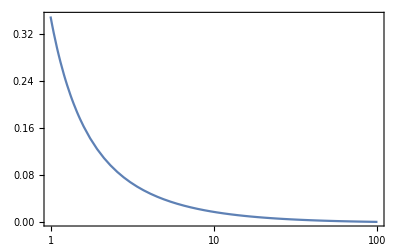
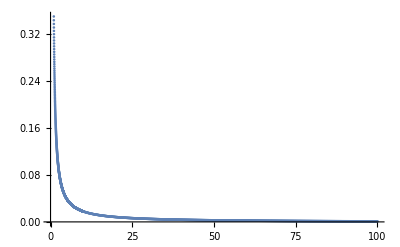

```mathematica
ScalarProfile[0.35,0.2298,3]
```

```mathematica
IntOut[0.35,0.2298,3,1,10^-4,200]
```

0.0000359565

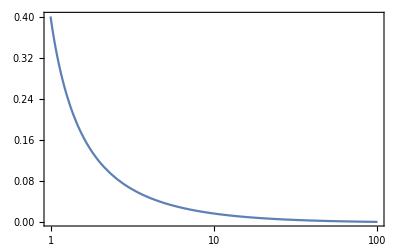
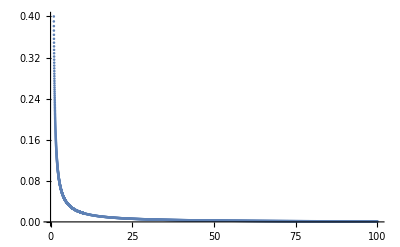

```mathematica
ScalarProfile[0.4,0.177917,0]
```

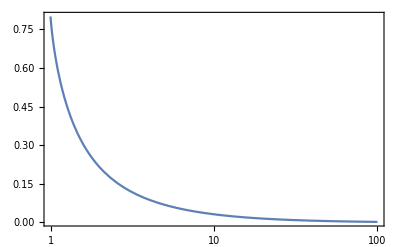
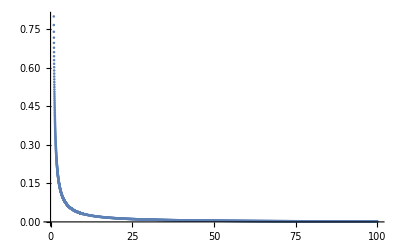

```mathematica
ScalarProfile[0.8,0.181002670,1]
```

#### for comparison with complex case for β=2 and τc =2ξc

```mathematica
ShootingAlpha[0.4,2,1,10^-4,200,0.24]
```

0.204236

7.35774×10^-10

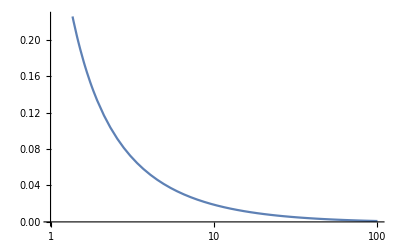

{1.09727,0.418395}

```mathematica
IntOut[0.4,0.20423637701281427,2,1,10^-4,200]
LogLinearPlot[{ϕ[r]/.SOLOUT},{r,rInit,100}]
{M,QS}
```

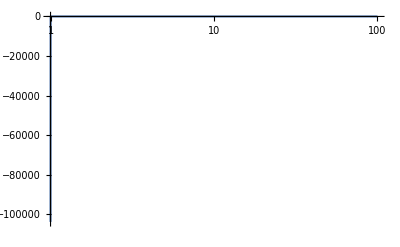
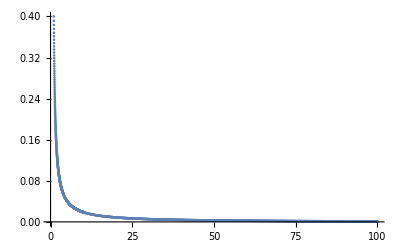

```mathematica
ScalarProfile[0.4,0.20423637701281427,2]
```

```mathematica
ShootingAlpha[0.2,2,1,10^-4,200,0.24]
```

0.18779

5.22844×10^-16

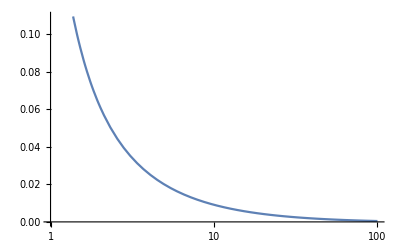

{1.15078,0.210749}

```mathematica
IntOut[0.2,0.1877901329511085,2,1,10^-4,200]
LogLinearPlot[{ϕ[r]/.SOLOUT},{r,rInit,100}]
{M,QS}
```

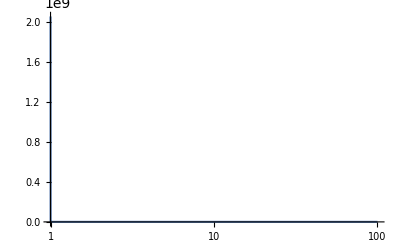
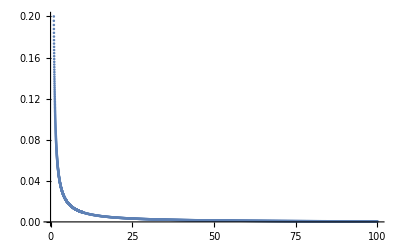

```mathematica
ScalarProfile[0.2,0.1877901329511085,2]
```

#### for comparison with complex case for β=2 and τc =5ξc

```mathematica
ShootingAlpha[0.5,2,1,10^-4,200,0.24]
```

0.215472

2.1343×10^-11

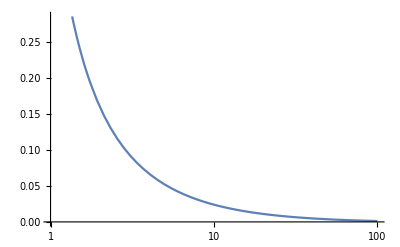

{1.06559,0.517794}

```mathematica
IntOut[0.5,0.21547168147333476,2,1,10^-4,200]
LogLinearPlot[{ϕ[r]/.SOLOUT},{r,rInit,100}]
{M,QS}
```

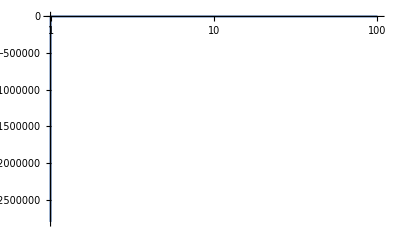
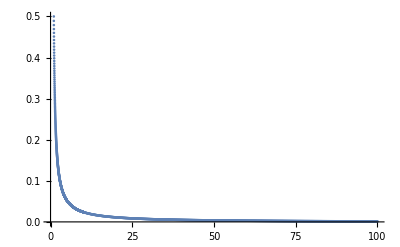

```mathematica
ScalarProfile[0.5,0.21547168147333476,2]
```

```mathematica
ShootingAlpha[0.1,2,1,10^-4,200,0.24]
```

0.183445

-9.75528×10^-12

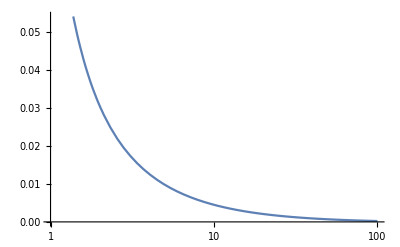

{1.16651,0.10543}

```mathematica
IntOut[0.1,0.183445471546575,2,1,10^-4,200]
LogLinearPlot[{ϕ[r]/.SOLOUT},{r,rInit,100}]
{M,QS}
```

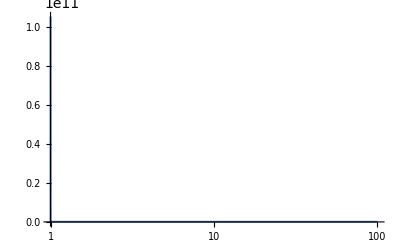
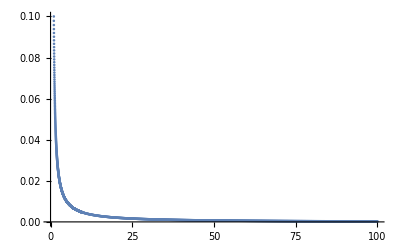

```mathematica
ScalarProfile[0.1,0.183445471546575,2]
```

### Q-M Plot

```mathematica
ScalarQM[2,0.25,0.19][[2]]//Timing
```

{1.94182,{1.13974,0.263259}}

```mathematica
Table[ScalarQM[2,phi,0.18][[2]],{phi,0.01,1.1,0.05}]
```

```mathematica
beta2={{1.172032610416619,0.010544370858583986},{1.1701046182237853,0.06326597208512631},{1.1654819980204285,0.11598221679240987},{1.1583111973213827,0.16867131526086182},{1.1488166829323119,0.2212829066503028},{1.1372917171809949,0.27372953289489943},{1.124085074494833,0.3258815925170778},{1.1095865556805358,0.3775658602136587},{1.0942114030181833,0.4285666333450925},{1.078385279446766,0.47862867622622535},{1.0625303165562563,0.5274609613742809},{1.0470533177243264,0.5747406428385257},{1.032335704528614,0.6201164998318164},{1.0187256497847845,0.6632118549047638},{1.0065314453051586,0.7036262906142048},{0.9960161754435441,0.7409354890935562},{0.9873905829575169,0.7746863355035797},{0.9808108025394016,0.8043798598877636},{0.9763701178751971,0.8294122716902307},{0.9741045332225625,0.8488120884749744},{0.975445906452439+0.0029893150364875467 ⅈ,0.8709684234665109+0.01730484594492264 ⅈ}}
```

{{1.17203,0.0105444},{1.1701,0.063266},{1.16548,0.115982},{1.15831,0.168671},{1.14882,0.221283},{1.13729,0.27373},{1.12409,0.325882},{1.10959,0.377566},{1.09421,0.428567},{1.07839,0.478629},{1.06253,0.527461},{1.04705,0.574741},{1.03234,0.620116},{1.01873,0.663212},{1.00653,0.703626},{0.996016,0.740935},{0.987391,0.774686},{0.980811,0.80438},{0.97637,0.829412},{0.974105,0.848812},{0.975446+0.00298932 ⅈ,0.870968+0.0173048 ⅈ}}

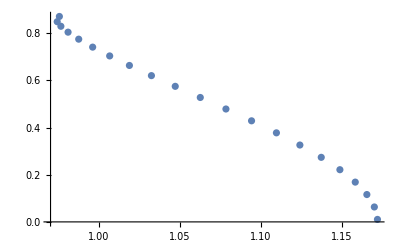

```mathematica
ListPlot[Re[beta2],PlotRange->All]
```

```mathematica
?ShootingAlpha
```

```mathematica
ShootingAlpha[0.68,5,1,10^-4,200,0.55]
```

0.598903

```mathematica
Table[ScalarQM[5,phi,0.18][[2]],{phi,0.005,0.3,0.05}]
```

{{1.17197,0.00527233},{1.1585,0.0581757},{1.1245,0.111834},{1.07462,0.166409},{1.01481,0.221501},{0.950811,0.276377}}

```mathematica
Table[ScalarQM[5,phi,0.3][[2]],{phi,0.3,0.4,0.05}]
```

{{0.893464,0.324897},{0.833035,0.377089},{0.778117,0.426698}}

```mathematica
Table[ScalarQM[5,phi,0.45][[2]],{phi,0.4,0.6,0.05}]
```

{{0.778117,0.426698},{0.729972,0.472921},{0.689268,0.514922},{0.65628,0.551848},{0.630985,0.582874}}

```mathematica
Table[ScalarQM[5,phi,0.55][[2]],{phi,0.61,0.7,0.05}]
```

{{0.626829,0.588307},{0.610353,0.611376}}

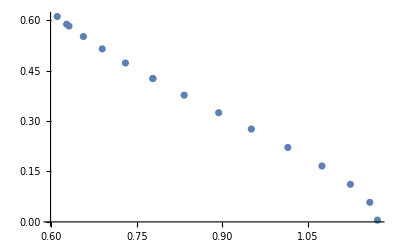

```mathematica
beta5 = {{1.1719739944204228,0.005272329017024186},{1.1585043841819795,0.05817573423281447},{1.124502120527149,0.11183370887828722},{1.0746183568728962,0.1664090443764215},{1.0148069495006593,0.2215006675799253},{0.9508114617952316,0.2763771721621645},{0.8934640977001975,0.3248968776510397},{0.8330351192091625,0.37708877759209125},{0.7781168995351145,0.4266983716378088},{0.778116899424709,0.42669837164724983},{0.7299718371267061,0.4729205147874423},{0.6892684913425244,0.5149219689277448},{0.6562795164722918,0.5518479022557822},{0.6309849983216962,0.5828744277393373},{0.6268287585128322,0.5883074872797291},{0.6103531301892684,0.6113762134757269}};
ListPlot[beta5]
```

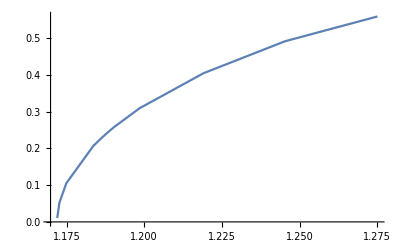

```mathematica
beta0 = {{1.1720108132908136,0.010543105078117614},{1.172733708686149,0.05268706278301319},{1.1749417969153502,0.10518998242661007},{1.1838188919554051,0.2089043613644037},{1.1839205535969286,0.20891313930114447},{1.185132116130344,0.21914134447414826},{1.1864024980769177,0.2293366578240717},{1.1877316521094894,0.23949723397819564},{1.1891195439134692,0.249621184190185},{1.1905660909527103,0.2597065604327492},{1.1985388675736093,0.3094568598742871},{1.219117995016245,0.40477649331464427},{1.2452841710989389,0.4915440682639897},{1.2750399576197726,0.5590842911328002}};
ListPlot[beta0,Joined->True,PlotRange->All]
```

```mathematica
beta3={{0.7880295403338337,0.7778795451418876},{0.7993589813703064,0.7441967934820526},{0.8259188920345977,0.688151660174656},{0.868113898907911,0.6133614807940445},{0.9239008512848469,0.5241070433468697},{0.9888592279236071,0.42481777741569665},{1.022680930937384,0.372743038079493},{1.0559379602958558,0.31971089663208896},{1.1155678876315964,0.21248563893160546},{1.1571360948033562,0.10570003342166047},{1.1682958872990978,0.05275588768304007},{1.1719355263842235,0.010544648242599597}}
```

{{0.78803,0.77788},{0.799359,0.744197},{0.825919,0.688152},{0.868114,0.613361},{0.923901,0.524107},{0.988859,0.424818},{1.02268,0.372743},{1.05594,0.319711},{1.11557,0.212486},{1.15714,0.1057},{1.1683,0.0527559},{1.17194,0.0105446}}

```mathematica
beta1={{1.2192657838366312,0.7311041263596345},{1.2065389583639519,0.6691457860855043},{1.1959998349606542,0.5912943803888339},{1.1816362281167478,0.41023000291817946},{1.1742977930514034,0.20948924867624255},{1.1726287229180838,0.10527023696124953},{1.1720932768569927,0.010544197610084108}}
```

{{1.21927,0.731104},{1.20654,0.669146},{1.196,0.591294},{1.18164,0.41023},{1.1743,0.209489},{1.17263,0.10527},{1.17209,0.0105442}}

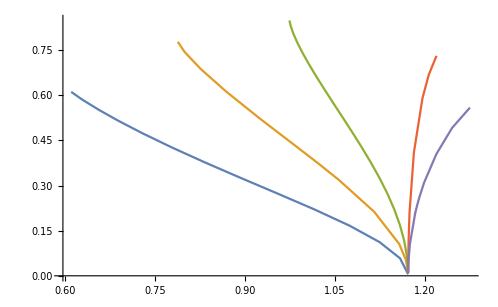

```mathematica
ListPlot[{beta5,beta3,beta2,beta1,beta0},Joined->True,PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["Plots/beta0.txt",beta0,"Table"]
Export["Plots/beta1.txt",beta1,"Table"]
Export["Plots/beta2.txt",beta2,"Table"]
Export["Plots/beta3.txt",beta3,"Table"]
Export["Plots/beta5.txt",beta5,"Table"]
```

Plots/beta0.txt

Plots/beta1.txt

Plots/beta2.txt

Plots/beta3.txt

Plots/beta5.txt

## Numerical Integration - “Algebraic”

Same as before, but here the equations to solve are the one given by the algebraically solved system, i.e. a second order ODE for the field and two first order ODEs for the metric functions. Here the initial conditions for σ are taken at the first order. One can check the result of the two integrations coincide.

Solving algebraically the system of field equations, one can get directly a system of one second order and two first order ODEs.

```mathematica
Clear[A,B,ϕ,σ,ρ,x,y]
rhc=1;
δ=10^-4;
rInit = rhc+δ;
rMax=200;
AlgebSystem=Solve[(FieldEqs/.TrasfAB)==0,{ϕ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;3]]/.{Rule->Subtract};
```

```mathematica
IntOut[ϕc_?NumericQ,αc_?NumericQ,βc_]:=(
Par = {r->rInit,rh->rhc,Subscript[f, 0]->ϕc,α->αc,β->βc,ϕh->ϕc};
BOUND =
{
ϕ[rInit] ==  ϕc,
ϕ'[rInit] ==  PhiPrimeHorizon,
A[rInit] == Subscript[a, 1](rInit-rhc),
B[rInit]==grrInit
}/.Par;
EQS = {AlgebSystem =={0,0,0}}/.{α->αc,β-> βc,η->1};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->1},EQS],{A,B,ϕ},{r,rInit,rMax}][[1]];
ϕINF = Re[ϕ[rMax]]/.SOLOUT;
InfRatio = (A[rMax]grr[rMax])^-1/.SOLOUT/.{α->αc,β->βc};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->InfRatio},EQS],{A,B,ϕ},{r,rInit,rMax}][[1]];
QS = SCharge[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT;
M=BHMass[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT;
ϕINF
)


ShootingPhi[α_,β_,guess_]:=(InfPhiPhi[f_?NumericQ]:=IntOut[f,α,β];
f/.FindRoot[InfPhiPhi[f],{f,guess},PrecisionGoal->4]
)
ShootingAlpha[ϕh_?NumericQ,β_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
InfPhiAlpha[f_?NumericQ]:=IntOut[ϕh,f,β];
f/.FindRoot[IntOut[ϕh,f,β],{f,guess},PrecisionGoal->4]
)
ScalarProfileSHOOT[phic_,βc_,guess_]:=(
a = ShootingAlpha[phic,βc,guess];
Points1 = Table[{r,ϕ[r]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,ϕ[r]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_Field.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[ϕ[r]/.SOLOUT,{r,1,100},PlotRange->All],
ListPlot[Points,PlotRange->All]}
)

ScalarProfile[phic_,αc_,βc_]:=(
IntOut[phic,αc,βc];
Points1 = Table[{r,Re[ϕ[r]]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,ϕ[r]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_Field.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[Re[ϕ[r]]/.SOLOUT,{r,rInit,100},PlotRange->All]
,ListPlot[Points,PlotRange->All]}
)

ScalarQM[β_,ϕc_,guess_]:=(
a=ShootingAlpha[ϕc,β,guess];
{{a},{M,QS}}
)
```

### Scalar FIeld Profile

```mathematica
Clear[A,B,ϕ,x,y,α,β]
```

```mathematica
AlphaValues[0.2,5]
```

AlphaValues[0.2,5]

-4.02646×10^-7

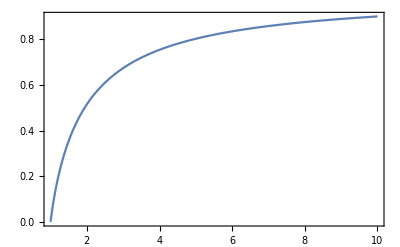

```mathematica
IntOut[1,0.264873,2]
Plot[Abs[A[r]]/.SOLOUT,{r,1,10}]
```

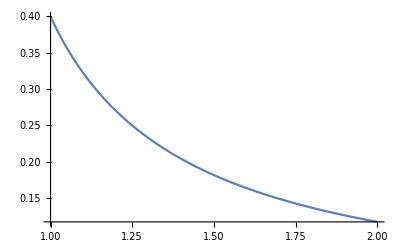

```mathematica
Plot[Abs[ϕ[r]]/.SOLOUT,{r,rInit,2}]
```

```mathematica
ShootingAlpha[0.03,30,0.18]
```

0.227187

```mathematica
ShootingAlpha[0.03,30,1.2]
```

1.37967

```mathematica
ShootingAlpha[0.03,30,3.0]
```

3.32099

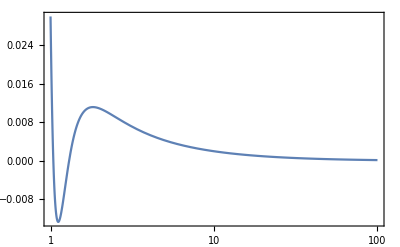
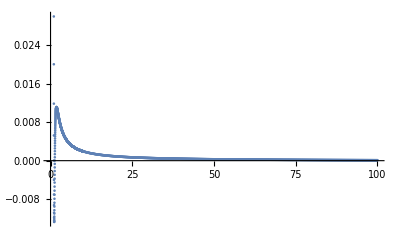

```mathematica
ScalarProfile[0.03,3.320993448218399,30]
```

```mathematica
M/.SOLOUT
```

0.274266

```mathematica
M/.SOLOUT
```

0.424772

```mathematica
M/.SOLOUT
```

1.04568

```mathematica
IntOut[0.35,0.2298,3]
```

0.0000358213

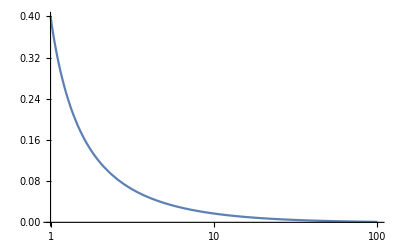
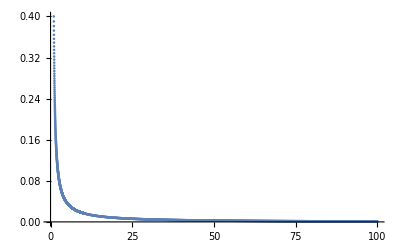

```mathematica
ScalarProfile[0.4,0.177917,0]
```

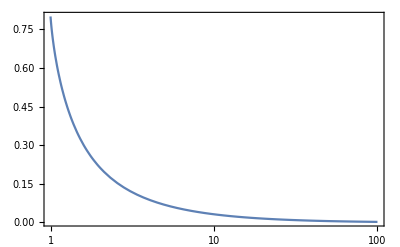
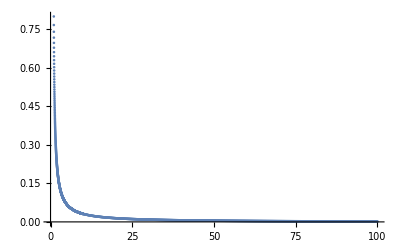

```mathematica
ScalarProfile[0.8,0.181002670,1]
```

### Q-M Plot

```mathematica
ScalarQM[2,0.2,0.26]
```

{{0.18779},{1.15088,0.210757}}

```mathematica
Table[ScalarQM[2,phi,0.26][[2]],{phi,0.01,1.1,0.02}]
```

{{1.17202,0.0105436},{1.17158,0.0316309},{1.1707,0.0527182},{1.16938,0.0738048},{1.16764,0.0948908},{1.16547,0.115975},{1.1629,0.137054},{1.15993,0.158127},{1.15658,0.17919},{1.15287,0.200239},{1.14881,0.221267},{1.14442,0.242271},{1.13973,0.263243},{1.13476,0.28417},{1.12954,0.305046},{1.12408,0.325861},{1.11841,0.3466},{1.11256,0.367252},{1.10656,0.387804},{1.10043,0.408238},{1.0942,0.42854},{1.0879,0.448691},{1.08156,0.468678},{1.0752,0.488477},{1.06884,0.508071},{1.06252,0.527437},{1.05627,0.546556},{1.0501,0.565417},{1.04404,0.583976},{1.03811,0.602218},{1.03234,0.620125},{1.02675,0.637668},{1.02135,0.654814},{1.01617,0.671549},{1.01123,0.687838},{1.00654,0.703661},{1.00211,0.718983},{0.997982,0.733785},{0.994141,0.748023},{0.990611,0.761687},{0.987399,0.774732},{0.984515,0.787129},{0.981967,0.798841},{0.979759,0.809838},{0.977895,0.820056},{0.976379,0.829464},{0.975211,0.837988},{0.974392,0.845518},{0.973924,0.851879},{0.97383+0.0000182122 ⅈ,0.856419+0.00045321 ⅈ},{0.974058+0.00031946 ⅈ,0.860186+0.00314729 ⅈ},{0.974509+0.00102813 ⅈ,0.86413+0.00766346 ⅈ},{0.975115+0.00220478 ⅈ,0.868544+0.0137342 ⅈ},{0.978819+0.00366609 ⅈ,0.87811+0.0173736 ⅈ},{0.989469+0.00484596 ⅈ,0.892937+0.0134686 ⅈ}}

```mathematica
beta2={{1.1720218734521641,0.010543627813693935},{1.171582778237915,0.03163090772820384},{1.1706993352692923,0.05271824699610003},{1.1693821355363376,0.07380482588223657},{1.1676374996751286,0.09489082860079166},{1.165472753706739,0.11597452659731992},{1.1628993603612754,0.13705398859408094},{1.159930077647983,0.1581267219224886},{1.1565803304312985,0.1791898822688261},{1.1528666413594257,0.20023863354191115},{1.1488067794338273,0.2212671689072119},{1.144422927026697,0.24227141696654517},{1.1397347471611616,0.26324253268867454},{1.1347643091222952,0.28416980838350114},{1.1295366152192743,0.3050461049279562},{1.1240768567939101,0.32586131981765776},{1.1184094725007503,0.3466001734312719},{1.1125615235581274,0.3672524118976208},{1.1065601440560353,0.3878043511402383},{1.100431239450904,0.40823771916077906},{1.0942035238710663,0.4285399565147449},{1.0879024125996466,0.4486914641715586},{1.0815589827126224,0.46867786913691867},{1.0751965417962157,0.48847669737828414},{1.0688432967276673,0.5080707304470276},{1.0625249409117303,0.5274371727990452},{1.0562673139660963,0.54655571443102},{1.0500988339187853,0.5654169947096869},{1.044037459471179,0.5839759584247983},{1.0381096305152893,0.602218369139595},{1.0323385128757885,0.6201248390695969},{1.0267452773706736,0.6376680331540363},{1.0213488605543497,0.6548143860376474},{1.0161706673835915,0.6715490831907287},{1.0112278635663767,0.6878377700109465},{1.006538933503453,0.7036607271942015},{1.0021136935769601,0.7189833373566763},{0.9979821691719977,0.7337851218998822},{0.9941412626902518,0.748022772850418},{0.9906111755584468,0.7616872642827245},{0.9873992608668822,0.7747324327520246},{0.9845154602993758,0.7871292688032977},{0.9819666245062291,0.798841345436339},{0.9797593815946662,0.8098377401302908},{0.9778952812741419,0.8200562522312858},{0.9763789376208393,0.8294636324564209},{0.9752111444909921,0.837987610638735},{0.9743915506902782,0.8455184457511415},{0.9739244224520863,0.8518788523325994},{0.9738297672807642+0.000018212245725391682 ⅈ,0.8564194701888519+0.00045320996381848535 ⅈ},{0.9740577529193832+0.0003194599808801197 ⅈ,0.8601861467213632+0.0031472939649959597 ⅈ},{0.9745090532106885+0.0010281277352707993 ⅈ,0.8641304659031304+0.007663455844861047 ⅈ},{0.9751145091931834+0.002204776292467356 ⅈ,0.86854350775599+0.013734161840595376 ⅈ},{0.9788192506202154+0.003666094594438774 ⅈ,0.8781099658988716+0.017373587394633315 ⅈ},{0.9894693185190571+0.004845955989980285 ⅈ,0.892936877935796+0.01346858764687314 ⅈ}};
```

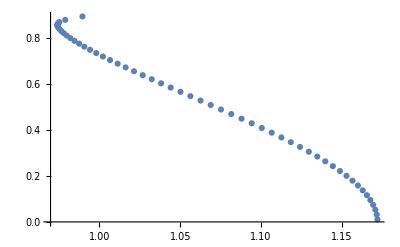

```mathematica
ListPlot[Re[beta2],PlotRange->All]
```

```mathematica
ShootingAlpha[0.68,5,0.55]
```

0.598903

```mathematica
Table[ScalarQM[5,phi,0.55][[2]],{phi,0.005,0.7,0.01}]
```

NDSolve::ndsz: At r == 1.01869, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At r == 1.01869, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.00223, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{{1.17197,0.00527234},{1.17106,0.0158204},{1.16925,0.0263787},{1.16654,0.0369535},{1.16295,0.0475508},{1.15851,0.0581757},{1.15323,0.0688327},{1.14716,0.0795252},{1.14032,0.0902555},{1.13275,0.101025},{1.12451,0.111834},{1.11562,0.122681},{1.10614,0.133566},{1.09611,0.144484},{1.08559,0.155433},{1.07463,0.166409},{1.06327,0.177407},{1.05156,0.18842},{1.03955,0.199445},{1.02729,0.210474},{1.01482,0.221501},{1.00219,0.232519},{0.98944,0.243523},{0.976605,0.254505},{0.963725,0.265459},{0.950832,0.276377},{0.937961,0.287254},{0.925141,0.298082},{0.912399,0.308855},{0.899762,0.319566},{0.887251,0.33021},{0.87489,0.340778},{0.862697,0.351266},{0.850691,0.361666},{0.838886,0.371973},{0.827298,0.382179},{0.81594,0.392279},{0.804822,0.402266},{0.793956,0.412134},{0.783351,0.421876},{0.773015,0.431487},{0.762956,0.440958},{0.753178,0.450284},{0.743689,0.459458},{0.734493,0.468474},{0.725595,0.477325},{0.716996,0.486003},{0.708701,0.494502},{0.700712,0.502815},{0.69303,0.510936},{0.685657,0.518857},{0.678594,0.526572},{0.671842,0.534073},{0.6654,0.541354},{0.659267,0.548408},{0.653444,0.555229},{0.647929,0.56181},{0.64272,0.568146},{0.637815,0.574231},{0.633212,0.580059},{0.628908,0.585624},{0.624899,0.590924},{0.621181,0.595952},{0.617749,0.600707},{0.6146,0.605184},{0.611726,0.609382},{0.609121,0.6133},{0.606779,0.616936},{0.604691,0.620292},{0.602848,0.623367}}

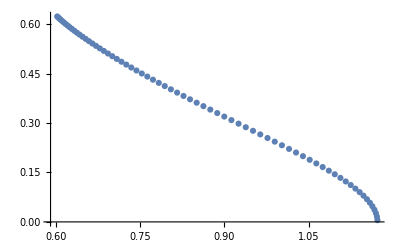

```mathematica
beta5 ={{1.1719736390053925,0.00527233625101873},{1.171062938991015,0.015820418287015577},{1.1692472051063751,0.02637865510780313},{1.166537324671445,0.03695347584257797},{1.1629496126016041,0.047550766824634334},{1.1585054655772622,0.05817573571168506},{1.1532311333925833,0.06883273916232933},{1.1471571780043852,0.0795251866891271},{1.1403189532625264,0.09025546163620374},{1.132754894616363,0.10102488603614918},{1.1245072453249878,0.11183371747136403},{1.1156198257439225,0.1226811779438034},{1.1061395983944695,0.13356550721881005},{1.0961147831307096,0.14448403688388695},{1.0855945749073856,0.15543328793057531},{1.0746286327283947,0.16640904276271953},{1.0632665653572417,0.17740650069003921},{1.0515574615724261,0.18842030856043274},{1.0395494663405327,0.1994447050157336},{1.0272894368277472,0.2104736073026324},{1.0148226516315608,0.22150066371834135},{1.0021925003784224,0.23251936990243152},{0.9894403486494384,0.24352308515683602},{0.9766053797855166,0.2545051080071996},{0.9637245083632554,0.2654587106096663},{0.9508323527208802,0.2763771712562282},{0.9379611047352567,0.2872537914455674},{0.9251407934271587,0.2980819185030992},{0.9123990915920746,0.3088549493347457},{0.8997615042211237,0.3195663346113124},{0.887251430035808,0.3302095704769779},{0.8748902868276449,0.3407782206073672},{0.8626974732943051,0.3512658679049894},{0.8506907670713896,0.36166613304525985},{0.8388861525763288,0.37197265526190565},{0.8272980752794603,0.3821790814220884},{0.8159395255846376,0.3922790542987533},{0.8048221463928531,0.40226620124103185},{0.7939563677186499,0.41213412081000306},{0.7833513827221821,0.4218763836721098},{0.7730152429352591,0.4314865086844928},{0.7629555375430489,0.4409579685014997},{0.7531784152411559,0.45028417895769424},{0.7436894698647504,0.4594584989418798},{0.7344934649432941,0.46847423012687506},{0.7255945055883959,0.47732461875966964},{0.7169960657582695,0.4860028609843138},{0.7087010594123953,0.4945021129414953},{0.7007117780011626,0.502815493348964},{0.6930300822649451,0.5109361106641622},{0.6856573027157814,0.5188570723226005},{0.67859438688179,0.5265715082286437},{0.6718417707099192,0.5340725900649016},{0.6653995102022907,0.5413535857162366},{0.6592671752209062,0.5484078455620511},{0.6534439978462532,0.5552288836298424},{0.6479287546237662,0.5618103962479074},{0.6427197882196655,0.5681463121336873},{0.63781506470647,0.5742308415151447},{0.633212056788125,0.5800585279849683},{0.6289077360353789,0.5856243075973999},{0.6248986298599506,0.5909235652777205},{0.6211807308393965,0.5959521984904667},{0.6177494777353122,0.6007066795604455},{0.6145997120810127,0.6051841241562209},{0.6117257225867702,0.6093823493531784},{0.6091210128670047,0.6132999412822316},{0.606779390539181,0.6169363096548823},{0.6046910398423476,0.6202917183183512},{0.6028480016653597,0.6233673624780156}};
ListPlot[beta5]
```

```mathematica
ScalarQM[0,0.2,0.26]
```

{{0.180954},{1.18391,0.208899}}

```mathematica
Table[ScalarQM[0,phi,0.19][[2]],{phi,0.005,0.6,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{1.17208,0.00527176},{1.17214,0.0158146},{1.17226,0.0263552},{1.17286,0.0368931},{1.17268,0.0474243},{1.17298,0.0579497},{1.17333,0.068467},{1.17374,0.0789749},{1.17422,0.0894715},{1.17475,0.0999562},{1.17534,0.110427},{1.17599,0.120881},{1.1767,0.131319},{1.17748,0.141739},{1.1783,0.152138},{1.17917,0.162515},{1.18012,0.172869},{1.18114,0.183198},{1.1822,0.1935},{1.18333,0.203773},{1.18451,0.214016},{1.18575,0.224228},{1.18705,0.234405},{1.18841,0.244547},{1.18983,0.254652},{1.1913,0.264717},{1.19284,0.27474},{1.19443,0.284719},{1.19608,0.294653},{1.19779,0.304538},{1.19956,0.314373},{1.20138,0.324156},{1.20327,0.333884},{1.20521,0.343553},{1.20721,0.353161},{1.20927,0.362705},{1.21138,0.372184},{1.21358,0.381592},{1.21578,0.390927},{1.21807,0.400186},{1.22041,0.409363},{1.22281,0.418457},{1.22527,0.427461},{1.22778,0.436367},{1.23034,0.445177},{1.23296,0.453882},{1.23563,0.462472},{1.23836,0.470946},{1.24113,0.479292},{1.24396,0.487501},{1.24683,0.49556},{1.24976,0.503461},{1.25272,0.511184},{1.25573,0.518713},{1.25876,0.526021},{1.26183,0.533076},{1.2649,0.53983},{1.26797,0.546199},{1.27094,0.551998},{1.27367+0.0000193699 ⅈ,0.556789+0.000422342 ⅈ}}

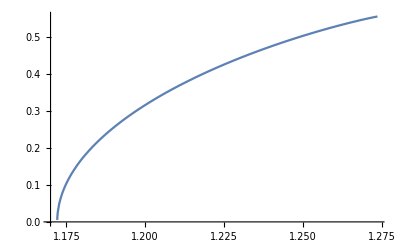

```mathematica
beta0 ={{1.172083015620685,0.005271761894537763},{1.1721441676266646,0.01581464125736598},{1.1722622162707743,0.02635521845363523},{1.172677435018334,0.04742434726391249},{1.1729777008099416,0.05794970146768522},{1.1733285308735275,0.0684669730915123},{1.1737430888842206,0.07897489107974402},{1.174216120125446,0.0894715443061601},{1.1747496851718504,0.09995618629845199},{1.1753417291575219,0.1104268039335718},{1.1759924210956259,0.12088143069473968},{1.1767022687866788,0.13131877870985678},{1.1774785700476884,0.1417385099050868},{1.178300418728885,0.1521376093795933},{1.1791728126533003,0.16251484971513638},{1.1801188150806783,0.17286881416352537},{1.1811401440232008,0.18319809318750033},{1.182204684255588,0.19350041630270381},{1.1833277033295255,0.20377341743538538},{1.1845095479553664,0.21401637554866806},{1.1857503833190548,0.22422769903749376},{1.1870502363951847,0.23440533421700205},{1.188408915944025,0.24454739137378484},{1.189826420357475,0.25465218014541924},{1.1913020612327467,0.26471669791166796},{1.1928365326674544,0.27474015214841174},{1.1944296183178345,0.2847194859847838},{1.1960808052940908,0.2946527467087795},{1.1977904747453851,0.30453831201287024},{1.1995585940661486,0.31437348180817387},{1.2013847806870257,0.324156085835024},{1.2032690999808981,0.333883535271699},{1.2052112803684694,0.343552628997134},{1.2072108279714884,0.35316050375404023},{1.2092682197948823,0.3627054021865687},{1.2113831777407922,0.37218356205136466},{1.2135758807967434,0.3815923242990451},{1.2157845419837647,0.39092694449764265},{1.2180705113976942,0.4001855404301866},{1.220413032716624,0.4093633015173522},{1.2228119809489861,0.41845700013346904},{1.2252662205020612,0.4274605517573673},{1.2277754080625818,0.43636683315119484},{1.2303402409109532,0.4451773749643289},{1.2329592880790534,0.45388182335108124},{1.2356310466982936,0.4624718447535147},{1.2383556294257354,0.4709455910772778},{1.2411328879538162,0.47929156546519747},{1.243959038453675,0.48750112491839215},{1.246834376402618,0.4955597983132646},{1.2497559475262445,0.5034605199144573},{1.2527207058403145,0.5111839604644031},{1.255725162471821,0.5187129090176309},{1.2587634045265084,0.5260207956926662},{1.2618275331503048,0.5330759367266962},{1.2649039732917666,0.5398299862586858},{1.2679659430662864,0.5461990169626108},{1.2709429790630191,0.5519981540087728},{1.2736707160892629,0.5567889257080268}};
ListPlot[beta0,Joined->True,PlotRange->All]
```

```mathematica
ScalarQM[3,0.9,0.36]
```

{{0.380397},{0.788016,0.777881}}

```mathematica
Table[ScalarQM[3,phi,0.36][[2]],{phi,0.005,1.1,0.01}]
```

{{1.17205,0.00527223},{1.17174,0.0158175},{1.17114,0.0263652},{1.17023,0.0369171},{1.16901,0.0474746},{1.1675,0.0580392},{1.1657,0.0686122},{1.16361,0.0791948},{1.16123,0.0897881},{1.15857,0.100393},{1.15564,0.11101},{1.15244,0.12164},{1.14898,0.132283},{1.14527,0.142939},{1.14131,0.153608},{1.13712,0.164289},{1.1327,0.174982},{1.12806,0.185686},{1.12321,0.1964},{1.11817,0.207122},{1.11294,0.217851},{1.10753,0.228585},{1.10196,0.239323},{1.09623,0.250062},{1.09035,0.260799},{1.08435,0.271532},{1.07822,0.282259},{1.07198,0.292977},{1.06563,0.303683},{1.0592,0.314373},{1.05269,0.325044},{1.04611,0.335694},{1.03948,0.346318},{1.03279,0.356913},{1.02607,0.367475},{1.01933,0.378001},{1.01256,0.388488},{1.00579,0.39893},{0.99902,0.409324},{0.992259,0.419667},{0.985518,0.429954},{0.978805,0.440181},{0.972127,0.450344},{0.965493,0.46044},{0.95891,0.470462},{0.952386,0.480409},{0.945927,0.490275},{0.939541,0.500055},{0.933234,0.509747},{0.927012,0.519345},{0.920881,0.528844},{0.914846,0.538242},{0.908914,0.547533},{0.903089,0.556712},{0.897376,0.565776},{0.89178,0.57472},{0.886305,0.583539},{0.880955,0.59223},{0.875734,0.600786},{0.870647,0.609205},{0.865695,0.617482},{0.860882,0.625611},{0.856211,0.633589},{0.851686,0.641411},{0.847309,0.649073},{0.843082,0.65657},{0.839007,0.663898},{0.835085,0.671052},{0.831319,0.678029},{0.827709,0.684824},{0.824257,0.691433},{0.820964,0.697851},{0.81783,0.704076},{0.814856,0.710103},{0.812042,0.715927},{0.809388,0.721547},{0.806888,0.726957},{0.804551,0.732154},{0.802317,0.737136},{0.800311,0.741899},{0.798412,0.746439},{0.796699,0.750754},{0.79514,0.754841},{0.793728,0.758697},{0.792467,0.762319},{0.791349,0.765704},{0.790365,0.768847},{0.789524,0.771746},{0.788835,0.774394},{0.788258,0.776785}}

```mathematica
beta3={{1.1720495050135007,0.005272231063096833},{1.1717448358513038,0.015817498996704576},{1.171136209015676,0.026365249536158392},{1.1702250403425594,0.03691709358844026},{1.1690136235394097,0.047474576671961075},{1.1675044790323377,0.05803915243704519},{1.1657011687384857,0.06861216133163343},{1.163607810665503,0.07919480679461216},{1.161229164555677,0.08978814019446564},{1.1585706143605436,0.10039303785965695},{1.155638147389669,0.11101018027100856},{1.152438326956636,0.12164005205337156},{1.148978266948026,0.13228292067057357},{1.1452656029672519,0.14293883039501878},{1.1413084568040337,0.1536076035039468},{1.1371154085616297,0.1642888244173431},{1.1326954535612102,0.17498184855880797},{1.1280575154031636,0.1856857979350977},{1.1232126679708452,0.19639956179488915},{1.1181695865483394,0.20712181471801597},{1.1129389993059218,0.21785098590034352},{1.1075314164719856,0.22858534879637663},{1.1019575347504142,0.23932291907037626},{1.0962281617375986,0.2500615438419892},{1.0903542559918302,0.26079887867835694},{1.084346810018978,0.2715324076293736},{1.0782161764169258,0.2822594514588798},{1.0719753935406005,0.2929771771528786},{1.0656334327483499,0.3036826124082536},{1.0592018967841068,0.31437264849249136},{1.0526915895064923,0.32504406078973297},{1.046113201291206,0.33569350723929015},{1.039477273763655,0.3463175441898724},{1.032794171186703,0.35691263326448813},{1.0260740711642093,0.36747514947474835},{1.0193269386195347,0.3780013885540505},{1.0125625127623674,0.38848757379497756},{1.0057903149004859,0.39892985883108106},{0.999019552894787,0.40932434658506384},{0.9922592140074792,0.4196670749418407},{0.9855180655754721,0.42995403357650347},{0.9788045344290724,0.4401811655959944},{0.9721267916682751,0.4503443705083071},{0.9654927276267402,0.46043950757316526},{0.9589099501853389,0.4704623986043589},{0.9523857842262424,0.4804088304628922},{0.9459272721004833,0.49027455729426345},{0.9395412035851451,0.5000553060621133},{0.9332340039229087,0.5097467648305561},{0.9270119067364112,0.5193446044135732},{0.9208808144641736,0.5288444597973831},{0.9148464500027281,0.5382419643064995},{0.9089141817728302,0.5475327083804465},{0.9030891436984539,0.5567122693983331},{0.8973762158834039,0.5657762077253982},{0.8917800230279334,0.5747200682743643},{0.8863049417209654,0.5835393833145228},{0.8809551028586531,0.5922296753863103},{0.8757344295483386,0.600786462784725},{0.8706465075348232,0.6092052541996953},{0.8656947873128096,0.6174815660983277},{0.8608824546281078,0.6256109183570815},{0.8562113509257717,0.6335888413725574},{0.8516864354570567,0.6414108814603267},{0.8473090959204862,0.6490726067665281},{0.8430816106834873,0.6565696136518784},{0.8390068790021289,0.6638975317469935},{0.8350850283637918,0.6710520385195733},{0.8313185148591683,0.6780288564357194},{0.8277086794926022,0.6848237680752827},{0.8242567370946264,0.6914326228557889},{0.8209635678711661,0.697851345731713},{0.8178298507297468,0.7040759458457632},{0.8148560222320381,0.7101025250600751},{0.8120422941954551,0.7159272859819181},{0.809388454062153,0.7215465395646492},{0.8068882818838125,0.7269567111708239},{0.804551085818682,0.732154344154839},{0.8023168700305324,0.7371360980884013},{0.8003107879450498,0.7418987547968955},{0.7984119829293708,0.7464392003243951},{0.7966992131274245,0.7507544145047736},{0.7951395797470001,0.7548414390060441},{0.793727582135829,0.7586973290630684},{0.7924672175257645,0.7623190893404951},{0.7913486191003825,0.7657035543744356},{0.790365253054506,0.7688472038207228},{0.7895244842974762,0.771745883508216},{0.7888345714496471,0.7743942934534386},{0.7882575592934029,0.7767850635187333}};
```

```mathematica
ScalarQM[1,0.5,0.19]
```

{{0.182407},{1.18778,0.504058}}

```mathematica
Table[ScalarQM[1,phi,0.19][[2]],{phi,0.005,0.8,0.01}]
```

{{1.17208,0.00527178},{1.17209,0.0158149},{1.17211,0.0263563},{1.17214,0.0368952},{1.17219,0.0474306},{1.17224,0.0579609},{1.17231,0.068486},{1.17238,0.0790042},{1.17247,0.0895141},{1.17257,0.100016},{1.17268,0.110508},{1.17279,0.120988},{1.17293,0.131456},{1.17307,0.141912},{1.17322,0.152353},{1.17339,0.162778},{1.17357,0.173188},{1.17376,0.18358},{1.17396,0.193954},{1.17418,0.204307},{1.1744,0.214639},{1.17464,0.224949},{1.1749,0.235237},{1.17516,0.2455},{1.17544,0.255737},{1.17573,0.265948},{1.17604,0.276131},{1.17636,0.286284},{1.17669,0.296406},{1.17704,0.306497},{1.1774,0.316556},{1.17778,0.32658},{1.17817,0.336568},{1.17858,0.34652},{1.17901,0.356433},{1.17945,0.366307},{1.1799,0.376138},{1.18037,0.385926},{1.18086,0.395672},{1.18137,0.405372},{1.18189,0.415025},{1.18243,0.42463},{1.18299,0.43418},{1.18357,0.443683},{1.18416,0.453131},{1.18478,0.462524},{1.18541,0.471861},{1.18606,0.481138},{1.18674,0.490353},{1.18743,0.499505},{1.18814,0.508594},{1.18888,0.517615},{1.18963,0.526568},{1.19041,0.535449},{1.19121,0.544257},{1.19203,0.552989},{1.19287,0.56164},{1.19373,0.570213},{1.19462,0.5787},{1.19553,0.587101},{1.19646,0.595411},{1.19742,0.603628},{1.1984,0.611749},{1.19941,0.619767},{1.20044,0.627684},{1.20149,0.635492},{1.20257,0.643189},{1.20367,0.650755},{1.2048,0.658205},{1.20595,0.665527},{1.20713,0.672711},{1.20833,0.679731},{1.20955,0.686615},{1.2108,0.693324},{1.21207,0.699843},{1.21336,0.706171},{1.21467,0.71228},{1.21599,0.718124},{1.21731,0.723653},{1.21863,0.728792}}

```mathematica
beta1={{1.1720779269763384,0.005271783572363188},{1.1720896314172702,0.015814874148376068},{1.1721107587029502,0.026356297429292706},{1.1721444395447211,0.03689521706200732},{1.1721868271666527,0.047430647849436895},{1.1722394859270542,0.057960862869301064},{1.172305328598311,0.06848599788326812},{1.1723812156478814,0.07900417516345012},{1.1724670641966422,0.08951406771422322},{1.1725660032049139,0.10001591735686038},{1.1726751125088584,0.11050759485323892},{1.1727948167482596,0.12098764743311276},{1.1729270802629397,0.13145649045460406},{1.1730699637353554,0.141911619137178},{1.1732246415937615,0.15235274723492037},{1.1733910219545525,0.16277849108173875},{1.1735693178027333,0.17318796886900448},{1.1737599249021615,0.1835803033953537},{1.1739624651071083,0.1939537914026482},{1.1741768589705905,0.20430665164867368},{1.1744036863239575,0.21463892112363747},{1.1746434310462839,0.22494928538458492},{1.1748960584701427,0.23523661209877125},{1.17516180994802,0.24549967322383556},{1.1754408194285122,0.2557373073072088},{1.1757333001552261,0.26594823903867243},{1.1760394162031984,0.2761311969164179},{1.1763590399560575,0.2862838756173284},{1.1766926324307343,0.29640619692996056},{1.1770408054165198,0.30649745480441426},{1.1774036805156245,0.31655560275375494},{1.1777813674872237,0.3265795833789829},{1.1781742112602154,0.3365680648093222},{1.1785824362284238,0.34651973984337797},{1.179006290193711,0.3564331245656597},{1.1794459949299838,0.366306743644097},{1.1799015740720686,0.37613796886138884},{1.180373272699595,0.3859264825110588},{1.1808621218486561,0.3956718324241584},{1.1813682425085434,0.40537209753092535},{1.18189169639277,0.4150254781386192},{1.1824327603727107,0.4246302179204025},{1.1829903751773174,0.4341801517352541},{1.1835677195682979,0.44368320675892314},{1.1841631475853713,0.4531313235260781},{1.1847775473307194,0.4625244121198774},{1.1854111381953818,0.4718605854842928},{1.1860641237110434,0.48113762266769805},{1.186736598106068,0.49035305254607336},{1.187429065119715,0.49950491807370084},{1.188142587356057,0.508594022832636},{1.188876456753959,0.5176151636312155},{1.1896314293066128,0.5265678144246173},{1.190407690338234,0.5354490536181687},{1.1912057544323682,0.5442572090958057},{1.1920256186813636,0.5529889444198829},{1.1928672675982321,0.5616402923813576},{1.1937320085137433,0.5702125089955621},{1.1946193529402573,0.5787002394376382},{1.195529822283252,0.587100971534793},{1.1964635901760872,0.5954114569370483},{1.1974207195882502,0.6036279658663873},{1.1984019034010898,0.6117485296585493},{1.1994068282277641,0.6197671512468957},{1.2004366645194158,0.6276842039111973},{1.2014909689189208,0.6354924073696423},{1.2025701594601426,0.6431887361296179},{1.2036712523993538,0.6507548118026003},{1.204799029798336,0.6582053041885861},{1.2059520703968893,0.6655274745479889},{1.2071296064792123,0.6727110172081581},{1.2083270563028226,0.6797309387220462},{1.2095533157163958,0.6866154195876636},{1.210800755472104,0.6933242165901348},{1.2120684020486459,0.6998432996773044},{1.2133586604252486,0.7061714388362555},{1.2146678016669927,0.7122803455123308},{1.2159887093165311,0.7181240769915157},{1.2173146138940332,0.7236530722185417},{1.21863347363129,0.7287918641765845}};
```

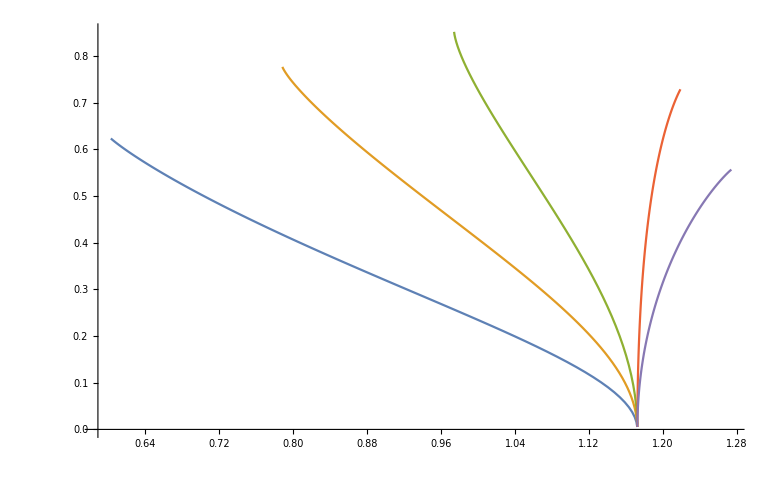

```mathematica
ListPlot[{beta5,beta3,beta2,beta1,beta0},Joined->True,PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
Export["Plots/beta0.txt",Re[beta0],"Table"]
Export["Plots/beta1.txt",Re[beta1],"Table"]
Export["Plots/beta2.txt",Re[beta2],"Table"]
Export["Plots/beta3.txt",Re[beta3],"Table"]
Export["Plots/beta5.txt",Re[beta5],"Table"]
```

Plots/beta0.txt

Plots/beta1.txt

Plots/beta2.txt

Plots/beta3.txt

Plots/beta5.txt

#### 1 nodes

```mathematica
ShootingAlpha[0.1,5,2.0]
```

1.14571

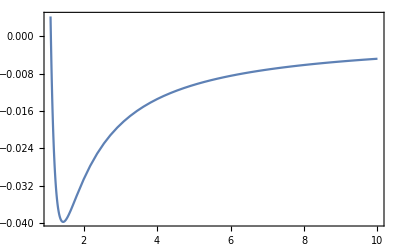

```mathematica
Plot[ϕ[r]/.SOLOUT,{r,1.1,10}]
```

```mathematica
Table[ScalarQM[5,phi,1.2][[2]],{phi,0.005,0.1,0.005}]
```

{{0.452482,-0.00252519},{0.452622,-0.00504633},{0.452855,-0.0075594},{0.45318,-0.0100603},{0.453596,-0.0125451},{0.454103,-0.0150095},{0.454699,-0.0174496},{0.455383,-0.019861},{0.456153,-0.0222397},{0.457007,-0.0245812},{0.457944,-0.0268812},{0.458961,-0.0291349},{0.460056,-0.0313377},{0.461225,-0.0334845},{0.462466,-0.0355696},{0.463775,-0.0375872},{0.465149,-0.0395304},{0.466584,-0.0413915},{0.468082,-0.0431609},{0.469607,-0.044827}}

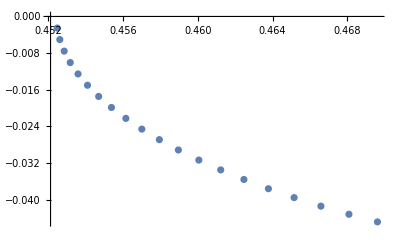

```mathematica
ListPlot[%]
```

```mathematica
ShootingAlpha[0.32,10,1.3]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.30899

```mathematica
Table[ScalarQM[10,phi,1.3][[2]],{phi,0.005,0.32,0.005}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.452406,-0.00252573},{0.452316,-0.00505067},{0.452168,-0.00757402},{0.451963,-0.0100949},{0.451702,-0.0126125},{0.451388,-0.0151256},{0.451024,-0.0176334},{0.450614,-0.0201344},{0.450161,-0.0226275},{0.449669,-0.0251112},{0.449143,-0.027584},{0.448587,-0.0300441},{0.448006,-0.0324898},{0.447405,-0.0349193},{0.44679,-0.0373306},{0.446164,-0.0397218},{0.445533,-0.0420907},{0.444901,-0.0444353},{0.444272,-0.0467535},{0.443652,-0.0490434},{0.443044,-0.0513027},{0.44245,-0.0535297},{0.441876,-0.0557224},{0.441323,-0.0578789},{0.440794,-0.0599975},{0.440292,-0.0620765},{0.439817,-0.0641144},{0.439372,-0.0661098},{0.438957,-0.0680612},{0.438574,-0.0699675},{0.438222,-0.0718276},{0.437902,-0.0736403},{0.437614,-0.0754047},{0.437358,-0.0771198},{0.437133,-0.0787849},{0.436938,-0.0803992},{0.436773,-0.0819618},{0.436637,-0.083472},{0.436527,-0.084929},{0.436445,-0.0863319},{0.436388,-0.0876798},{0.436357,-0.0889714},{0.436347,-0.0902055},{0.43636,-0.0913802},{0.436392,-0.0924932},{0.436444,-0.0935411},{0.436515,-0.0945192},{0.4366,-0.0954197},{0.436699,-0.0962271},{0.436808,-0.0968828},{0.436929-0.0000361489 ⅈ,-0.0974194-0.000185954 ⅈ},{0.437075-0.0000732909 ⅈ,-0.0979363-0.000468548 ⅈ},{0.437242-0.000114509 ⅈ,-0.0984547-0.000828502 ⅈ},{0.437416-0.000140131 ⅈ,-0.0989832-0.00124239 ⅈ},{0.437636-0.000167586 ⅈ,-0.0995248-0.0016948 ⅈ},{0.437826-0.000166575 ⅈ,-0.100081-0.00217472 ⅈ},{0.438031-0.000140996 ⅈ,-0.100653-0.0026738 ⅈ},{0.438258-0.000128358 ⅈ,-0.10124-0.00318537 ⅈ},{0.438479-0.000085191 ⅈ,-0.101845-0.00370393 ⅈ},{0.438695-0.0000240593 ⅈ,-0.102466-0.00422478 ⅈ},{0.438924+0.00005621 ⅈ,-0.103106-0.00474377 ⅈ},{0.439149+0.000167097 ⅈ,-0.103765-0.00525719 ⅈ},{0.439441+0.000289827 ⅈ,-0.104421-0.00570163 ⅈ},{0.440691+0.000459681 ⅈ,-0.104638-0.00532381 ⅈ}}

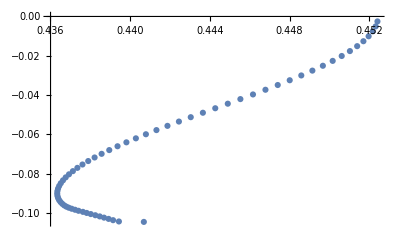

```mathematica
ListPlot[Re[%]]
```

```mathematica
ShootingAlpha[0.33,20,2.0]
```

2.16268

```mathematica
ShootingAlpha[0.31,20,2.0]
```

2.00797

```mathematica
Table[ScalarQM[20,phi,2.0][[2]],{phi,0.005,0.33,0.01}]
```

NDSolve::ndsz: At r == 1.21553, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At r == 1.21553, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.05696, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dprec: The precision of input value {200} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition (0.0002 (4.-20. (InterpolatingFunction[«1»][200.])^2))/(InterpolatingFunction[{{1.0001,1.00021}},{5,7,1,{70},{4},0,0,0,0,Automatic,«3»},{{«1»}},«1»,{Automatic}][200.] «1») is not a number or a rectangular array of numbers.

ReplaceAll::reps: {ϕ[10001/10000]==0.205,«3»,{-(2046.68 r ϕ[«1»]-4093.36 r B[«1»] ϕ[«1»]+«12»+«95»)/(Times[«3»]+Times[«4»]+Times[«4»]+Times[«4»]+«3»+Times[«4»]+Times[«4»]+Times[«4»]+«39»)+ϕ''[r],A'[r]+«1»,B'[r]+(r («1»))/(«1»)}=={0,0,0}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Re[InterpolatingFunction[{{1.0001,1.00021}},«3»,{Automatic}][200]]} is not a list of numbers with dimensions {1} at {f} = {2.66494}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
{{0.452103314367047,-0.002527867001416309},{0.4494718313323843,-0.007629845772468976},{0.4443609610374871,-0.012855125770075157},{0.43707640275772647,-0.018241767623398433},{0.42806195327891156,-0.023781899231744993},{0.9952502064073437,0.05994438713543481},{0.4070215984534749,-0.03511735594497259},{0.39608918283827854,-0.04076960789215656},{0.38549710197627707,-0.04631613305177943},{0.37556528389152566,-0.05169768585395313},{0.366498749769426,-0.05686878222235343},{0.3583950521035626,-0.06179759303307269},{0.3512733096153588,-0.06646428769689777},{0.3450966367837377,-0.07085885617378505},{0.33979296518102836,-0.07497871643957338},{0.33527604178430104,-0.078826666774544},{0.3314522527268875,-0.08240911028587351}}
```

{{0.452103,-0.00252787},{0.449472,-0.00762985},{0.444361,-0.0128551},{0.437076,-0.0182418},{0.428062,-0.0237819},{0.99525,0.0599444},{0.407022,-0.0351174},{0.396089,-0.0407696},{0.385497,-0.0463161},{0.375565,-0.0516977},{0.366499,-0.0568688},{0.358395,-0.0617976},{0.351273,-0.0664643},{0.345097,-0.0708589},{0.339793,-0.0749787},{0.335276,-0.0788267},{0.331452,-0.0824091}}

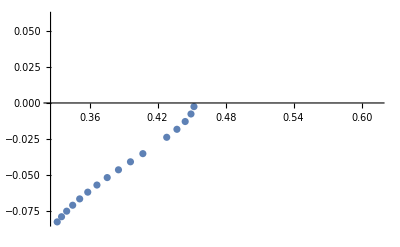

```mathematica
ListPlot[Re[%]]
```

### Stability

```mathematica
IntModes[αc_?NumericQ,βc_?NumericQ,ωc_?NumericQ]:=
(
EQSmode={(EigMode[ω,r]/.{α-> αc,β->βc,ϵ->1,ω->ωc}/.SOLOUT)==0};
BOUNDmodeIn = {ϕp[200]==0,ϕp'[200]==-1};
BOUNDmodeOut = {ϕp[1.0001]==0,ϕp'[1.0001]==1};
SOLMODEIn=NDSolve[Join[BOUNDmodeIn,EQSmode],{ϕp},{r,200,1+0.0001}][[1]];
SOLMODEOut=NDSolve[Join[BOUNDmodeOut,EQSmode],{ϕp},{r,1+0.0001,200}][[1]];
ϕpIN = ϕp[r]/.SOLMODEIn/.{r->50};
ϕpOUT = ϕp[r]/.SOLMODEOut/.{r->50};
ϕpINprime = ϕp'[r]/.SOLMODEIn/.{r->50};
ϕpOUTprime = ϕp'[r]/.SOLMODEOut/.{r->50};
W=(ϕpIN*ϕpOUTprime-ϕpOUT*ϕpINprime);
)

ShootingMode[ϕh_?NumericQ,α_?NumericQ,β_?NumericQ]:=(
Clear[f,InfMode];
IntOut[ϕh,α,β,1,10^-4,200];
InfMode[f_?NumericQ]:=IntModes[α,β,f];
f/.FindRoot[IntModes[α,β,f],{f,0.1},PrecisionGoal->4]
)
```

```mathematica
ShootingAlpha[0.5,0,0.2]
```

0.175723

```mathematica
ModeExplore[ϕi_,βc_,ωs_]:=(
alpha=ShootingAlpha[ϕi,βc,0.2];
IntOut[ϕi,alpha,βc];
IntModes[alpha,βc,ωs];
{Plot[{(ϕp[r]/.SOLMODEOut),(ϕp[r]/.SOLMODEIn)},{r,2,100}],
M,W})
```

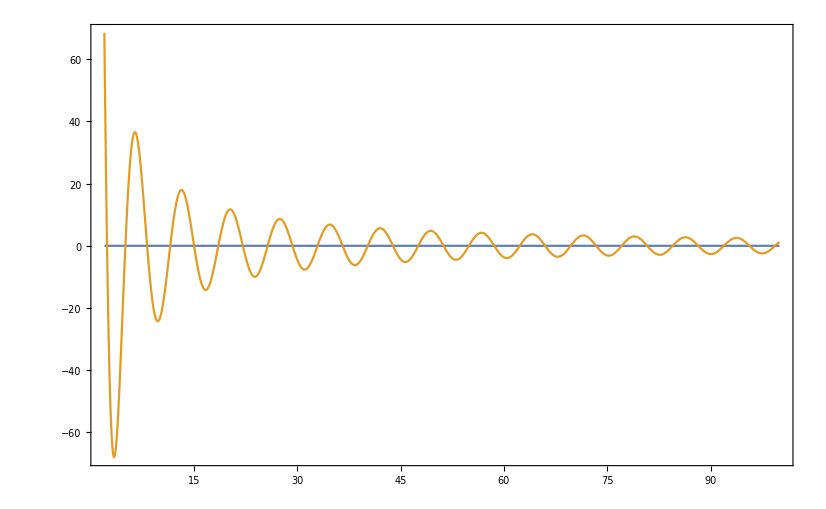
{-Graphics-,1.24544,-2.15804×10^-6}

```mathematica
ModeExplore[0.5,0,0.7]
```